```mathematica
Clear["Global`*"]
```

```mathematica
(*Parameters*)
Pv=2338;(*[Pa]*)
(*Pg0=1.55*10^6;*)
P0=10^5; (*[Pa] Атмосферное давление*)
σ=0.07286; (*[N/m] Коэффициент поверхностного натяжения*)
(*FIRST ATTEMPT*)
(*Rb0=100*10^-9; 
mg=7.74517*10^-20;*)
(*For the article_Static approach*)
(*Rb0=2.76153*10^-7; 
mg=6.56*10^-19; *)

(*For the article_Dynamic approach*)
Rb0=300*10^-9;
mg=7.84632*10^-19; 
(*mg=9.54*^-19;*)
Rl0=40*10^(-6); (*[m] Начальный радиус конфайнмента жидкости*)
Rg=287;(*[J/(kg*K)] Удельная газовая постоянная, Rg=R/M, М - молярная масса газа for dry air*)
T=293; (*[K] Температура системы*)
Ev=2.2*10^9; (*[Pa] Объемный модуль упругости*)
ρ0=1000;(*[kg/m^3] Fundamentals of Fluid Mechanics,Bruce R.Munson,6th Edition, at 20grad C, page 716*)
μ=10^-3;(*[kg/(m*s)]*)

(*Rb0=350*10^-9; 
mg=1.09777*10^-18;*)


(*Functions*)
(*Classical. Pressure without Pv:   Press[Rb_]=PL-Pv(T)   *)
(*Press[Rb_]:=-(2σ)/Rb+(3*mg*Rg*T)/(4*Pi*Rb^3);*)
(*#use it  Classical. Pressure with Pv*)
PressPv[Rb_]:=Pv-(2σ)/Rb+(3*mg*Rg*T)/(4*Pi*Rb^3);
(*Modified. Pressure without Pv:   PL1[Rb_]=PL1-Pv(T)*)
(*PL1[Rb_]:=-(2*σ)/Rb+(3*mg*Rg*T)/(4*Pi*Rb^3)-(Ev*(Rb^3-Rb0^3))/(Rl0^3-Rb0^3);*)
(*#use it Modified. Pressure with Pv*)
PL1Pv[Rl0_,Rb0_,Rb_]:=Pv-(2*σ)/Rb+(3*mg*Rg*T)/(4*Pi*Rb^3)-(Ev*(Rb^3-Rb0^3))/(Rl0^3-Rb0^3);

(*Solutions Subscript[P, L]=Pv-(2*σ)/Rb+(3*mg*Rg*T)/(4*Pi*Rb^3)-(Ev*(Rb^3-Rb0^3))/(Rl0^3-Rb0^3) for Rb*)
Reqright4[Rl0_,Rb0_,Pl1_]:=Rb/.Solve[{PL1Pv[Rl0,Rb0,Rb]==Pl1 },Rb][[4]];
Reqright5[Rl0_,Rb0_,Pl1_]:=Rb/.Solve[{PL1Pv[Rl0,Rb0,Rb]==Pl1 },Rb][[5]];
Reqright6[Rl0_,Rb0_,Pl1_]:=Rb/.Solve[{PL1Pv[Rl0,Rb0,Rb]==Pl1 },Rb][[6]];

(*Subscript[R, L1]*)
(*Subscript[R, L1] relative: (Subscript[R, L1]-Subscript[R, L0])/Subscript[R, L0]*)  RL1relat[Rl0_,Rb0_,Rb_]:=Chop[((Rb^3+(Rl0^3-Rb0^3)/Ev*(P0-Pv-(3*mg*Rg*T)/(4*Pi*Rb^3)+Ev+(2*σ)/Rb))^(1/3)-Rl0)/Rl0];
(*Subscript[R, L1][Rb_]*)  RL1[Rl0_,Rb0_,Rb_]:=Chop[(Rb^3+(Rl0^3-Rb0^3)/Ev*(P0-Pv-(3*mg*Rg*T)/(4*Pi*Rb^3)+Ev+(2*σ)/Rb))^(1/3)];
(*Subscript[R, L1][PL1_]*)  Rl1new[Rl0_,Rb0_,Pl1_]:=Chop[(Rl0^3+(P0-Pl1)*((Rl0^3-Rb0^3)/Ev))^(1/3)];

(*The points of transitions*)
RadiusB=Min[Rb/.Solve[{D[PL1Pv[Rl0,Rb0,Rb],Rb]==0,Rb≥0 },                           Element[Rb,Reals]](*[[1]]*)];
RadiusC=Max[Rb/.Solve[{PL1Pv[Rl0,Rb0,Rb]==PL1Pv[Rl0,Rb0,RadiusB],Rb≥0 },Element[Rb,Reals]]];
RadiusD=Max[Rb/.Solve[{D[PL1Pv[Rl0,Rb0,Rb],Rb]==0,Rb≥0 },                           Element[Rb,Reals]](*[[1]]*)];
RadiusA=Min[Rb/.Solve[{PL1Pv[Rl0,Rb0,Rb]==PL1Pv[Rl0,Rb0,RadiusD],Rb≥0 },Element[Rb,Reals]]];

(*Frequency in Herz: Classic and Modified*)
(*FreqCLASSRP[Rb_]:=Chop[1/(2Pi)*(1/(ρ0*Rb^2)*((9*mg*Rg*T)/(4*Pi*Rb^3)-(2*σ)/Rb))^(1/2)];
f1[Rl0_,Rb0_,Rb_]:=Chop[1/(2Pi)*(((5*(1-(Rb/RL1[Rl0,Rb0,Rb])^3)^3)/((1-(Rb0/RL1[Rl0,Rb0,Rb])^3)*(5-9*(Rb/RL1[Rl0,Rb0,Rb])+5*(Rb/RL1[Rl0,Rb0,Rb])^3-(Rb/RL1[Rl0,Rb0,Rb])^6)))*1/(ρ0*((Rl0^3-Rb0^3)/((RL1[Rl0,Rb0,Rb])^3-Rb0^3))*Rb^2)*(3*((3*mg*Rg*T)/(4*Pi*(Rb^3))+(Ev*Rb^3)/(Rl0^3-Rb0^3))-(2*σ)/Rb))^(1/2)]; *)




coef1=10^6;
coef12=10^-6;
coefp0Ev=10^6;
coefp012Ev=10^-6;


coefp0=1/P0;
coefp012=P0;

StringJoin["Mass of gas in the bubble mg=",ToString[mg*10^21"[zg]"]]
StringJoin["Radius of the initial bubble R_b0=",ToString[Rb0*10^9"[nm]"]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Mass of gas in the bubble mg=784.632 [zg]

Radius of the initial bubble R_b0=300 [nm]

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

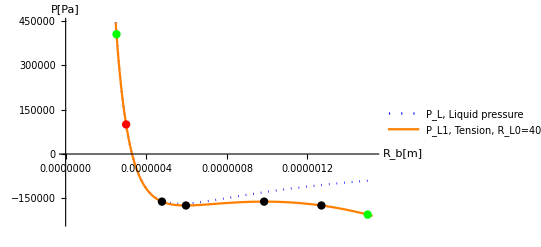

405000.  =Upper pressure

100000  =Middle (initial) pressure

-205000.  =Lower pressure

=Range of pressure

0.0000399982  =Radius of liquid cell for Upper pressure

0.00004  =Radius of liquid cell for Middle (initial) pressure

0.0000400018  =Radius of liquid cell for Lower pressure

Driving frequency fconf= 1000 kHz

Номер периода вынуждающей силы считается с 110 по 180

Всего периодов 71

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

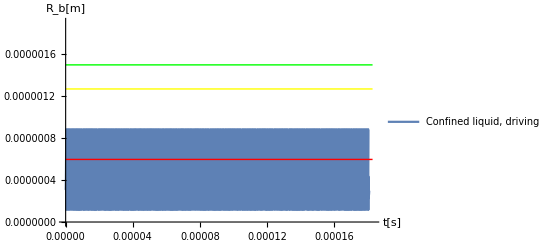

0.115372  =minimum radius R_(0  min)[μm]

0.88467  =maximum radius R_(0  max) [μm]

```mathematica
(*BULK LIQUID_sinusoidal (like tanh) driving force Subscript[P, L1]*)
(*Data for an initial expansion*)
pl1=P0 (*middle pressure*);
Text[" =The middle pressure, [Pa]"pl1];
(*Data for final expansion*)
pl11=4.05P0;(*amplitude pressure above middle*);
Text[" =The amplitude pressure above middle, [Pa]"pl11];
Ampl=1.0*(pl1-pl11)/pl1;
(*Frequency set*)
fbulk=52.7*10^4;(*[Hz]*)
fconf=1*10^6;(*[Hz]*)
k1=110; (*Number of the period initial*)
k2=180;(*Number of the period final*)
kappa=1.9*10^-5;(*m^2/s*)
Numbperiods=12(*10000*);
timeintegr=40/fconf(*500*10^-6*)(*Numbperiods/fconf*);(*100*10^-6*);(*certain interval of time for integration and plotting*)
Npoints=4000; (*number of points for plot*)
(*Triggers functions*)
(*Confined liquid sinus function for liquid element*)
Rl1[f_,t_]:=(Rl0^3+(P0-pl1*(1+Ampl*Sin[2Pi*f*t]))*((Rl0^3-Rb0^3)/Ev))^(1/3);
dRl1[f_,t_]:=-(2 Ampl *f* π pl1 (-Rb0^3+Rl0^3) Cos[2 f π* t])/(3 Ev (Rl0^3+((-Rb0^3+Rl0^3) (P0-pl1 (1+Ampl Sin[2 f π *t])))/Ev)^(2/3));  
d2Rl1[f_,t_]:=-(8 Ampl^2 f^2 π^2 pl1^2 (-Rb0^3+Rl0^3)^2 Cos[2 f π t]^2)/(9 Ev^2 (Rl0^3+((-Rb0^3+Rl0^3) (P0-pl1 (1+Ampl Sin[2 f π t])))/Ev)^(5/3))+(4 Ampl f^2 π^2 pl1 (-Rb0^3+Rl0^3) Sin[2 f π t])/(3 Ev (Rl0^3+((-Rb0^3+Rl0^3) (P0-pl1 (1+Ampl Sin[2 f π t])))/Ev)^(2/3));  


Φ[Rb_,Rl1_]:=(1-9/5*(Rb/Rl1)+(Rb/Rl1)^3-1/5*(Rb/Rl1)^6)/((1-(Rb/Rl1)^3)^2);
A1[Rb_,Rl1_]:=(2(Rb/Rl1)^2+8(Rb/Rl1)+5)/(((Rb/Rl1)^2+(Rb/Rl1)+1)*((Rb/Rl1)^3+3(Rb/Rl1)^2+6(Rb/Rl1)+5));
A2[Rb_,Rl1_]:=-(3(Rb/Rl1)*(2(Rb/Rl1)^2+8(Rb/Rl1)+5))/(((Rb/Rl1)^2+(Rb/Rl1)+1)*((Rb/Rl1)^3+3(Rb/Rl1)^2+6(Rb/Rl1)+5));
A3[Rb_,Rl1_]:=(3(Rb/Rl1)^2*(2(Rb/Rl1)^2+8(Rb/Rl1)+5))/(2((Rb/Rl1)^2+(Rb/Rl1)+1)*((Rb/Rl1)^3+3(Rb/Rl1)^2+6(Rb/Rl1)+5));
A4[Rb_,Rl1_]:=3/2*((Rb/Rl1)^2+3(Rb/Rl1)+1)/((Rb/Rl1)^3+3(Rb/Rl1)^2+6(Rb/Rl1)+5);


(*PLOT_Pressure from quasi-static model*)
Show[
Plot[{
PressPv[Rb],
PL1Pv[Rl0,Rb0,Rb]
},{Rb,0*10^6,1.2*RadiusC},
PlotRange->{-230000,445000},
GridLinesStyle->Directive[Dashed,Dashing[Tiny]],
LabelStyle->Directive[Black,Bold,16],
GridLines->{
{Reqright4[Rl0,Rb0,pl11],
Reqright4[Rl0,Rb0,pl1],
Reqright6[Rl0,Rb0,(1+Ampl)*pl1],
RadiusA,
RadiusB,
RadiusD,
RadiusC
},{
PL1Pv[Rl0,Rb0,RadiusA],
PL1Pv[Rl0,Rb0,RadiusB],
PL1Pv[Rl0,Rb0,RadiusD],
PL1Pv[Rl0,Rb0,RadiusC],
PL1Pv[Rl0,Rb0,Reqright4[Rl0,Rb0,pl1]],
PL1Pv[Rl0,Rb0,Reqright4[Rl0,Rb0,(1+Ampl)*pl1]],
PL1Pv[Rl0,Rb0,Reqright6[Rl0,Rb0,pl11]]
}},
PlotStyle->{
{Blue,Dotted,{Thickness[Large]}},
{Orange,{Thickness[Large]}}
},
Epilog->{
PointSize[0.015],
{Red,Point[{Rb0,P0}]},
{Green,Point[{Reqright4[Rl0,Rb0,pl11],pl11}]},
{Green,Point[{Reqright6[Rl0,Rb0,(1+Ampl)*pl1],(1+Ampl)*pl1}]},


(*{Black,Point[{Rb0,PL1Pv[Rl0,Rb0,Rb0]}]},*)
{Black,Point[{RadiusA,PL1Pv[Rl0,Rb0,RadiusA]}]},
{Black,Point[{RadiusB,PL1Pv[Rl0,Rb0,RadiusB]}]},
{Black,Point[{RadiusD,PL1Pv[Rl0,Rb0,RadiusD]}]},
{Black,Point[{RadiusC,PL1Pv[Rl0,Rb0,RadiusC]}]}(*,
{Green,Point[{RadiusD*coef1,coefp0*PressPv[RadiusD]}]},
{Red,Point[{RadiusC*coef1,coefp0*PressPv[RadiusC]}]}*)
},
PlotLegends->{
"P_L, Liquid pressure",
"P_L1, Tension, R_L0=40μm, R_b0=276nm, Yellow point is ''trigger point''"
},
AxesLabel->{"R_b[m]","P[Pa]"}]]


Text[(1-Ampl)*pl1 " =Upper pressure"]
Text[pl1 " =Middle (initial) pressure"]
Text[(1+Ampl)*pl1 " =Lower pressure"]
Text[" =Range of pressure"]

Text[Rl1new[Rl0,Rb0,pl1(1-Ampl)] " =Radius of liquid cell for Upper pressure"]
Text[Rl1new[Rl0,Rb0,pl1] " =Radius of liquid cell for Middle (initial) pressure"]
Text[Rl1new[Rl0,Rb0,pl1(1+Ampl)]" =Radius of liquid cell for Lower pressure"]

(*Text[fconf/fbulk" =Relationfconf/fbulk"]*)
(*Text[k2/fconf*1.0"   =timeintegr"]*)

StringJoin["Driving frequency fconf= ",ToString[fconf*10^-3 "kHz"]]


(*CONFINED LIQUID with dissipation on the walls- SINUS Function*)
ndsmod=ParametricNDSolve[{Φ[Rb[t],Rl1[f,t]]*(Rb[t]*Rb''[t]+3/2*(Rb'[t])^2*A1[Rb[t],Rl1[f,t]]+Rb'[t]*dRl1[f,t]*A2[Rb[t],Rl1[f,t]]+(dRl1[f,t])^2*A3[Rb[t],Rl1[f,t]]+Rl1[f,t]*d2Rl1[f,t]*A4[Rb[t],Rl1[f,t]])==1/(ρ0*((Rl0^3-Rb0^3)/(Rl1[f,t]^3-Rb[t]^3)))*((3*mg*Rg*T)/(4*Pi*(Rb[t])^3)+Pv-(2σ)/Rb[t]-P0+Ev*((Rl1[f,t])^3-(Rb[t])^3-Rl0^3+Rb0^3)/(Rl0^3-Rb0^3)-4*μ*(Rb'[t]/Rb[t]-dRl1[f,t]/Rl1[f,t])/(1-Rb[t]^3/(Rl1[f,t])^3)),Rb[0]==Rb0,Rb'[0]==0},Rb,{t,0,1.0*(k2+2)/f},{f},
(*WorkingPrecision->24*)(*PrecisionGoal->0,AccuracyGoal->0,MaxStepSize->10^-9,*)
(*Method->"BDF"*)Method->{"DoubleStep",Method->"StiffnessSwitching"},
InterpolationOrder->All];

StringJoin["Номер периода вынуждающей силы считается с ",ToString[k1], " по ", ToString[k2]]
StringJoin["Всего периодов ",ToString[k2-k1+1]]


(*Radius vs. time*)
Show[
Plot[{
(*Rb[fconf][t]/.ndsmod*)
Evaluate[Rb[fconf][t]/.ndsmod](*,
Rb[t]/.ndsmodconfdonw*)
},
{t,0,(k2+1)/fconf},
AxesLabel->{"t[s]","R_b[m]"},
LabelStyle->Directive[Black,Bold,16],
GridLinesStyle->Directive[Dashed],

(*General view*)

(*PlotRange->Full,*)
(*PlotRange->{{0,17*10^-6},{0.95Rb0*0,1.3RadiusC}},*)

PlotRange->{{0,(k2+3)/fconf(*timeintegr*)},{0.95Rb0*0,1.5RadiusC}},

(*PlotRange->{{0,5*10^-6},{0.95Rb0*0,1.2RadiusC}},*)
(*PlotRange->{{0*10^-6,1.5*10^-6},{0.95Rb0*0,1.15RadiusC}},*)
(*PlotRange->{{4.67*10^-6,4.78*10^-6(*0.2timeintegr*)},{0.95Rb0*0,2.09*10^-7(*29.5RadiusC*)}},*)
PlotStyle->{
Thickness[Large]
},
(*MaxRecursion->Infinity,*)
PlotPoints->IntegerPart[1.5*Npoints],
PlotLegends->{
(*StringJoin["Bulk liquid, driving freq [kHz] f=",ToString[fbulk*10^-3]],*)
StringJoin["Confined liquid, driving freq [kHz] f=",ToString[fconf*10^-3]](*,
StringJoin["Confined liquid, Delta functio",ToString[n]],
StringJoin["Non-cavitation regime, driving freq [kHz] f=",ToString[fconf*10^-3]]*)
},
PlotLegends->Automatic,
GridLines->{Table[k/fconf,{k,k1,k2}]
,{Rb0,
Max[s2["ValuesOnGrid"]],
Min[s2["ValuesOnGrid"]]
(*,
RadiusB, Rmean*)
(*Rb[fconf][1/fconf]/.ndsmod *)

(*Rb0,
Reqright4[Rl0,Rb0,pl11],
(*Reqright4[Rl0,Rb0,pl1] ,*)
Reqright6[Rl0,Rb0,(1+Ampl)*pl1],
RadiusA,
RadiusB*)

(*,RadiusD ,
Reqright4[Rl0,Rb0,press11],
Reqright4[Rl0,Rb0,press1] ,
Reqright4[Rl0,Rb0,(1+Amplsmall)*press1]*)
  }}
],
Graphics[{Red,Thickness[Large],Line[{{0,RadiusB},{(k2+3)/fconf,RadiusB}}]}],
Graphics[{Yellow,Thickness[Large],Line[{{0,RadiusC},{(k2+3)/fconf,RadiusC}}]}],
Graphics[{Green,Thickness[Large],Line[{{0,Reqright6[Rl0,Rb0,(1+Ampl)*pl1]},{(k2+3)/fconf,Reqright6[Rl0,Rb0,(1+Ampl)*pl1]}}]}]
](*,
Epilog-> {Red,PointSize[0.04],Point[FindPeaks[Table[Rb[t*10^-6]/.ndsmodconfdonw[[1]],{t,0,0.5timeintegr*10^6}]]]}*)



(*ω0[RL1_,Rb_]:=√((5(1-(Rb/RL1)^3)^2)/(5-9 Rb/RL1+5(Rb/RL1)^3-(Rb/RL1)^6)*3/(ρ0*(Rl0^3-Rb0^3)/(RL1^3-Rb^3)*Rb^2)*(3/(4Pi)*(mg*Rg*T)/Rb^3-(2σ)/(3Rb)+(Ev*Rb^3)/(Rl0^3-Rb0^3))) ;*)
(*Text[fconf*1.0*10^-6" =fconf [MHz]"]*)
s2=Rb[fconf]/.First@ndsmod;
Rmean=(Max[s2["ValuesOnGrid"]]+Min[s2["ValuesOnGrid"]])*0.5;
Text[" =minimum radius R_(0  min)[μm] "]  (Min[s2["ValuesOnGrid"]])*10^6
Text[" =maximum radius R_(0  max) [μm]"]  (Max[s2["ValuesOnGrid"]])*10^6
(*Text[" =mean radius SubscriptBox[(R),(0\mean)]=(SubscriptBox[R, 0 max] + SubscriptBox[R, 0 min])/2[μm] "]  Rmean*10^6
Text["AND"] 
Text[" =τ_thermal for minimum radius [ns] "]  (Min[s2["ValuesOnGrid"]])^2/kappa*10^9
Text[" =τ_thermal for maximum radius [ns]"]  (Max[s2["ValuesOnGrid"]])^2/kappa*10^9
Text[" =τ_thermal for mean radius [ns] "]  ( Rmean)^2/kappa*10^9
Text["AND"] 
Text[" =τ_(natural oscill) for minimum radius R_(0 min) [ns] "]  (2Pi)/ω0[RL1[Rl0,Rb0,Min[s2["ValuesOnGrid"]]],Min[s2["ValuesOnGrid"]]]*10^9
Text[" =τ_(natural oscill) for maximum radius R_(0 max) [ns]"]       (2Pi)/ω0[RL1[Rl0,Rb0,Max[s2["ValuesOnGrid"]]],Max[s2["ValuesOnGrid"]]]*10^9
Text[" =τ_(natural oscill) for mean radius R_(0 mean)=(R_(0 max))/2 [ns] "]  (2Pi)/ω0[RL1[Rl0,Rb0, Rmean], Rmean]*10^9
Plot[
ω0[RL1[Rl0,Rb0,Rb],Rb]
,{Rb,0,1.2Max[s2["ValuesOnGrid"]]},
GridLines->{{Max[s2["ValuesOnGrid"]]},{}}
]*)
```

Driving frequency fconf= 100 kHz

Номер периода вынуждающей силы считается с 30 по 34

Всего периодов 5

20000    =initial frequency [kHz]

60000    =final frequency [kHz]

500    =step of frequency [kHz]

81.    =Amount of periods [points on X-axis] of the external driving force

$Aborted

ListPlot::lpn: M is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot[M,AxesLabel→{f_ext[Hz],R_b[m]},LabelStyle→Directive[GrayLevel[0],12],GridLines→{{20000000,60000000},{5.96905×10^-7}},GridLinesStyle→Directive[Dashing[{Small,Small}]]]

100    =The external frequency fconf [kHz]

10.    =initial frequency [kHz]

20000    =final frequency [kHz]

30.    =step of frequency [kHz]

667.333    =Amount of periods [points on X-axis] of the external driving force

40    =Расчет начинается с этого номера периода вынуждающей силы

46    =Final number of periods of driving force we finish calculations

{3011.84,Null}

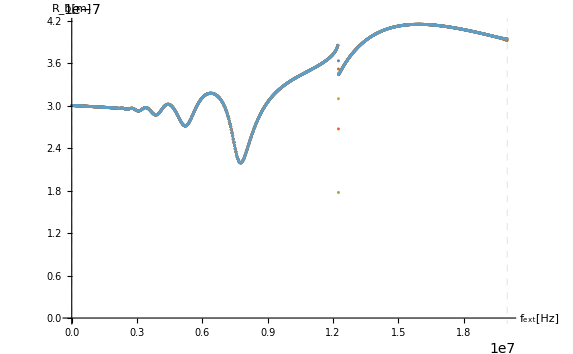

```mathematica
(*Bifurcation diagram*)
StringJoin["Driving frequency fconf= ",ToString[fconf*10^-3 "kHz"]]
StringJoin["Номер периода вынуждающей силы считается с ",ToString[k1], " по ", ToString[k2]]
StringJoin["Всего периодов ",ToString[k2-k1+1]]

freq1=200;
freq2=600;
stepfreq=5;



Text[freq1*fconf*10^-3"   =initial frequency [kHz]"]
Text[freq2*fconf*10^-3"   =final frequency [kHz]"]
Text[stepfreq*fconf*10^-3"   =step of frequency [kHz]"]
Text[(freq2-freq1+stepfreq)/(1.0stepfreq)"   =Amount of periods [points on X-axis] of the external driving force"]
(*Number of periods since m1 to m2*)
numperiodsinit=k1;
numperiodsfin=k2 ;


(*AbsoluteTiming[M=Table[Rb[i*fconf][j/(i*fconf)]/.ndsmod,{j,numperiodsinit,numperiodsfin},{i,freq1,freq2,stepfreq}];]*)
(*M=Table[{i,(Rb[i][j/i]/.ndsmod)},{j,numperiodsinit,numperiodsfin},{i,freq1*fconf,freq2*fconf,stepfreq*fconf}]*)


AbsoluteTiming[M=Table[{i,10^0*(Rb[i][j/i]/.ndsmod)},{j,numperiodsinit,numperiodsfin},{i,freq1*fconf,freq2*fconf,stepfreq*fconf}];]
(*MatrixForm[M,
TableHeadings->{
{
Column[Table[StringJoin["n-th number of period of ext driv force n=",ToString[k]],{k,m1,m2}]]

(*StringJoin["n-th number of period of ext driv force n=",ToString[m1]],
StringJoin["n-th number of period of ext driv force n=",ToString[m1+1]]*)
},
{

StringJoin["Ext freq[kHz]=",ToString[k1*fconf*10^-3]],
StringJoin["Ext freq[kHz]=",ToString[(k1+1)*fconf*10^-3]]
}
}
]*)


ListPlot[M,
AxesLabel->{"f_ext[Hz]","R_b[m]"},
LabelStyle->Directive[Black,12],
(*PlotStyle->{Black(*,PointSize[0.05/6]*)}*)
(*Frame->True,
FrameLabel->{"f_ext[MHz]","R_b[μm]"},*)
GridLines->{{freq1*fconf,freq2*fconf}
,{ 10^0*RadiusB }},
GridLinesStyle->Directive[Dashed]
]
(*/Bifurcation diagram*)
```

0.5    =initial frequency [kHz]

1000.    =final frequency [kHz]

0.5    =step of frequency [kHz]

2000.    =Amount of periods [points on X-axis] of the external driving force

Driving frequency fconf= kHz

Номер периода вынуждающей силы считается с 110 по 180

Всего периодов 71

{27000.7,Null}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

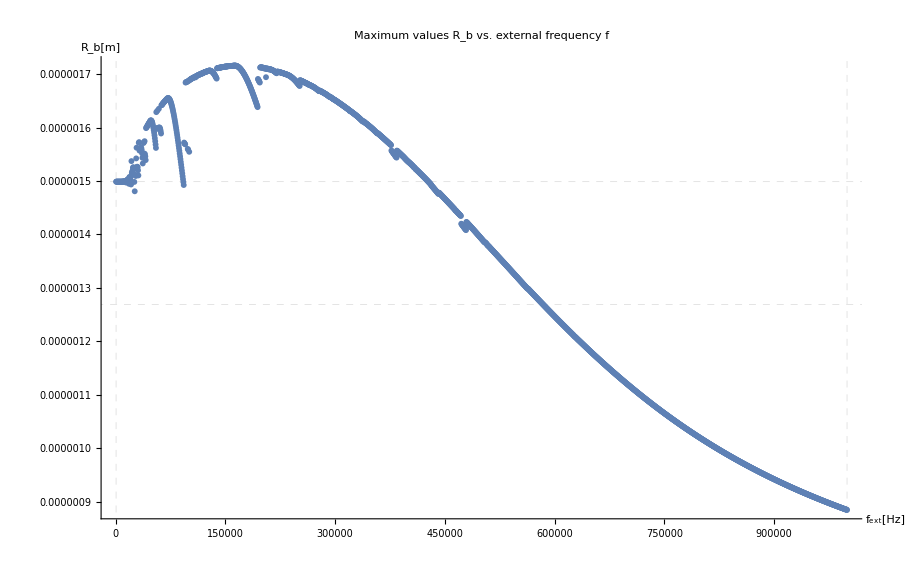

RadiusB= 0.596905 μm

RadiusC= 1.26903 μm

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Radius in final point= 1.4987 μm

1.    =initial frequency [kHz]

200.    =final frequency [kHz]

3.    =step of frequency [kHz]

67.3333    =Amount of periods [points on X-axis] of the external driving force

Driving frequency fconf= kHz

Номер периода вынуждающей силы считается с 110 по 180

Всего периодов 71

{2220.54,Null}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

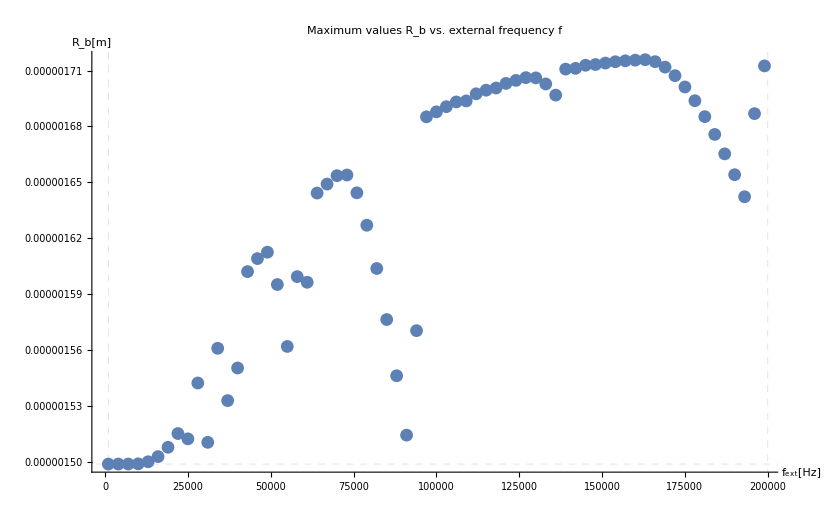

RadiusB= 0.596905 μm

RadiusC= 1.26903 μm

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Radius in final point= 1.4987 μm

```mathematica
(*Max Rb for bifurcation*)
fconf=1*10^3;(*Hz*)
freq1=0.5(*0.5*);
freq2=1000;
stepfreq=0.5;
numperiodsinit=k1;
numperiodsfin=k2 ;

Text[1.0freq1*fconf*10^-3"   =initial frequency [kHz]"]
Text[1.0freq2*fconf*10^-3"   =final frequency [kHz]"]
Text[1.0stepfreq*fconf*10^-3"   =step of frequency [kHz]"]
Text[(freq2-freq1+stepfreq)/(1.0stepfreq)"   =Amount of periods [points on X-axis] of the external driving force"]
StringJoin["Driving frequency fconf= ",ToString[fconf*10^-3 "kHz"]]
StringJoin["Номер периода вынуждающей силы считается с ",ToString[k1], " по ", ToString[k2]]
StringJoin["Всего периодов ",ToString[k2-k1+1]]

AbsoluteTiming[
MM=
Table[
{
i,(* NMaximize[Rb[i][t]/.ndsmod,{t,(k2-2)/i,k2/i}][[1]]*) NMaximize[{Rb[i][t]/.ndsmod,t≥ (k2-20.)/i,t≤ k2/i*1.},t][[1]]
},{i,freq1*fconf,freq2*fconf,stepfreq*fconf}
];
]

(*AbsoluteTiming[
MM=
Table[
{
i, Max[Table[Rb[i][j/i]/.ndsmod,{j,k2-3,k2,10^-3}]]
},{i,freq1*fconf,freq2*fconf,stepfreq*fconf}
];
]*)


(*MatrixForm[MM]*)

ListPlot[MM,
PlotLabel->"Maximum values R_b vs. external frequency f",
AxesLabel->{"f_ext[Hz]","R_b[m]"},
LabelStyle->Directive[Black,12],
(*PlotStyle->{Black(*,PointSize[0.05/6]*)}*)
(*Frame->True,
FrameLabel->{"f_ext[MHz]","R_b[μm]"},*)
GridLines->{{freq1*fconf,freq2*fconf}
,{ RadiusB ,Reqright6[Rl0,Rb0,(1+Ampl)*pl1],
RadiusC}},
GridLinesStyle->Directive[Dashed]
]

StringJoin["RadiusB= ",ToString[RadiusB*10^6"μm"]]
StringJoin["RadiusC= ",ToString[RadiusC*10^6"μm"]]
StringJoin["Radius in final point= ",ToString[Reqright6[Rl0,Rb0,(1+Ampl)*pl1]*10^6"μm" ]]




(*Как найти максимум*)
(*fconf1=10^3;
a=NMaximize[Rb[fconf1][t]/.ndsmod,{t,(k2-2)/fconf1,k2/fconf1}][[1]]
s2=Rb[fconf1]/.First@ndsmod;
b=Max[s2["ValuesOnGrid"]]
a-b*)


(*M=Table[{i,10^0*(Rb[i][j/i]/.ndsmod)},{j,numperiodsinit,numperiodsfin},{i,freq1*fconf,freq2*fconf,stepfreq*fconf}]*)
(*AbsoluteTiming[Maxim=Table[{i,Max[(Rb[i]/.First@ndsmod)["ValuesOnGrid"]]},(*{j,numperiodsinit,numperiodsfin},*){i,freq1*fconf,freq2*fconf,stepfreq*fconf}];]*)

(*MatrixForm[M,
TableHeadings->{
{
Column[Table[StringJoin["n-th number of period of ext driv force n=",ToString[k]],{k,m1,m2}]]

(*StringJoin["n-th number of period of ext driv force n=",ToString[m1]],
StringJoin["n-th number of period of ext driv force n=",ToString[m1+1]]*)
},
{

StringJoin["Ext freq[kHz]=",ToString[k1*fconf*10^-3]],
StringJoin["Ext freq[kHz]=",ToString[(k1+1)*fconf*10^-3]]
}
}
]*)


(*ListPlot[Maxim,
PlotLabel->"Maximum values R_b vs. external frequency f",
AxesLabel->{"f_ext[Hz]","R_b[m]"},
LabelStyle->Directive[Black,12],
(*PlotStyle->{Black(*,PointSize[0.05/6]*)}*)
(*Frame->True,
FrameLabel->{"f_ext[MHz]","R_b[μm]"},*)
GridLines->{{freq1*fconf,freq2*fconf}
,{ RadiusB ,
RadiusC}},
GridLinesStyle->Directive[Dashed]
]*)
```

37.0083

1.    =initial frequency [kHz]

100.    =final frequency [kHz]

3.    =step of frequency [kHz]

34.    =Amount of periods [points on X-axis] of the external driving force

Driving frequency fconf= kHz

Номер периода вынуждающей силы считается с 110 по 180

Всего периодов 71

{1747.26,Null}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

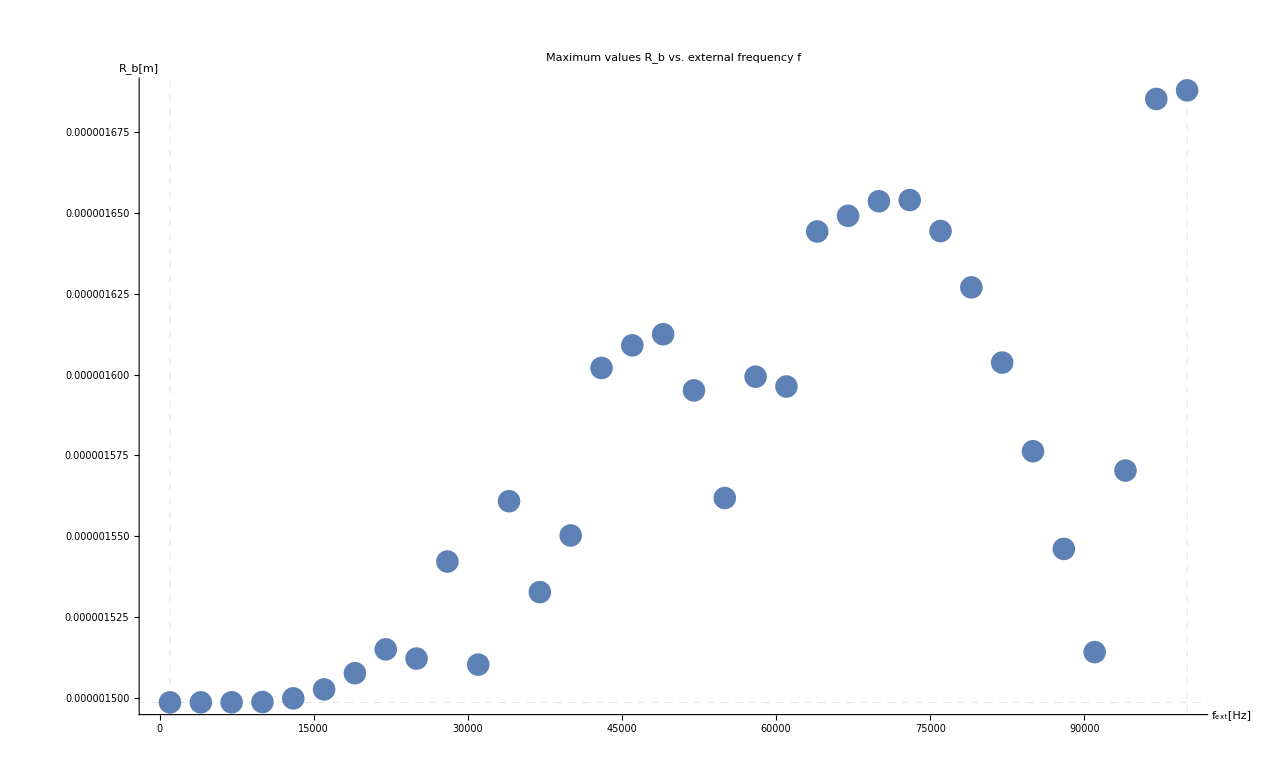

RadiusB= 0.596905 μm

RadiusC= 1.26903 μm

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Radius in final point= 1.4987 μm

1.    =initial frequency [kHz]

100.    =final frequency [kHz]

30.    =step of frequency [kHz]

4.3    =Amount of periods [points on X-axis] of the external driving force

Driving frequency fconf= kHz

Номер периода вынуждающей силы считается с 110 по 180

Всего периодов 71

{564.272,Null}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

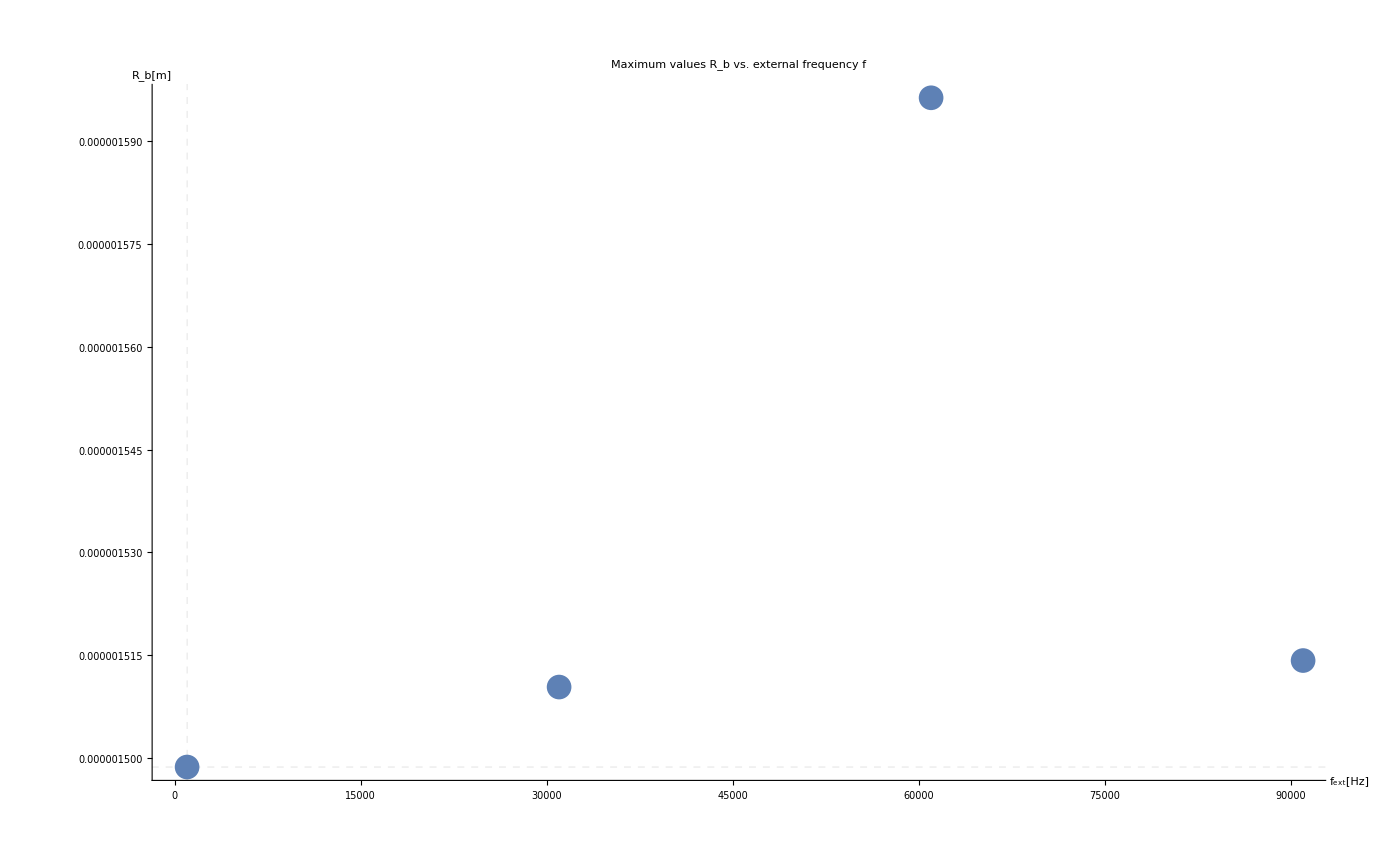

RadiusB= 0.596905 μm

RadiusC= 1.26903 μm

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Radius in final point= 1.4987 μm

0.01    =initial frequency [kHz]

50000.    =final frequency [kHz]

30.    =step of frequency [kHz]

1667.67    =Amount of periods [points on X-axis] of the external driving force

Driving frequency fconf= kHz

Номер периода вынуждающей силы считается с 110 по 180

Всего периодов 71

{2889.94,Null}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

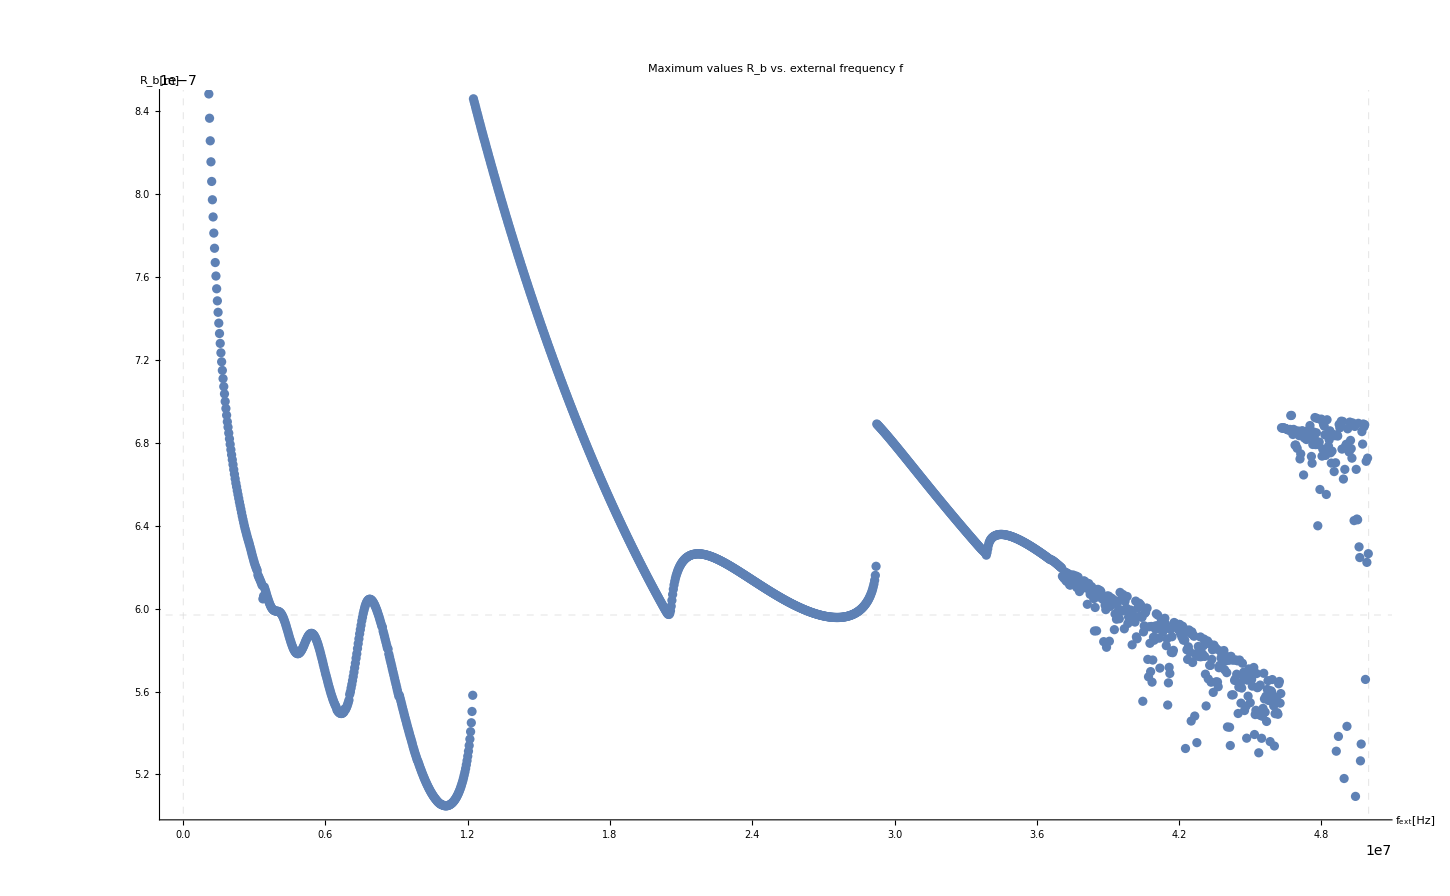

RadiusB= 0.596905 μm

RadiusC= 1.26903 μm

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Radius in final point= 1.4987 μm

0.1    =initial frequency [kHz]

40000.    =final frequency [kHz]

30.    =step of frequency [kHz]

1334.33    =Amount of periods [points on X-axis] of the external driving force

Driving frequency fconf= kHz

Номер периода вынуждающей силы считается с 110 по 130

Всего периодов 21

{1993.73,Null}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

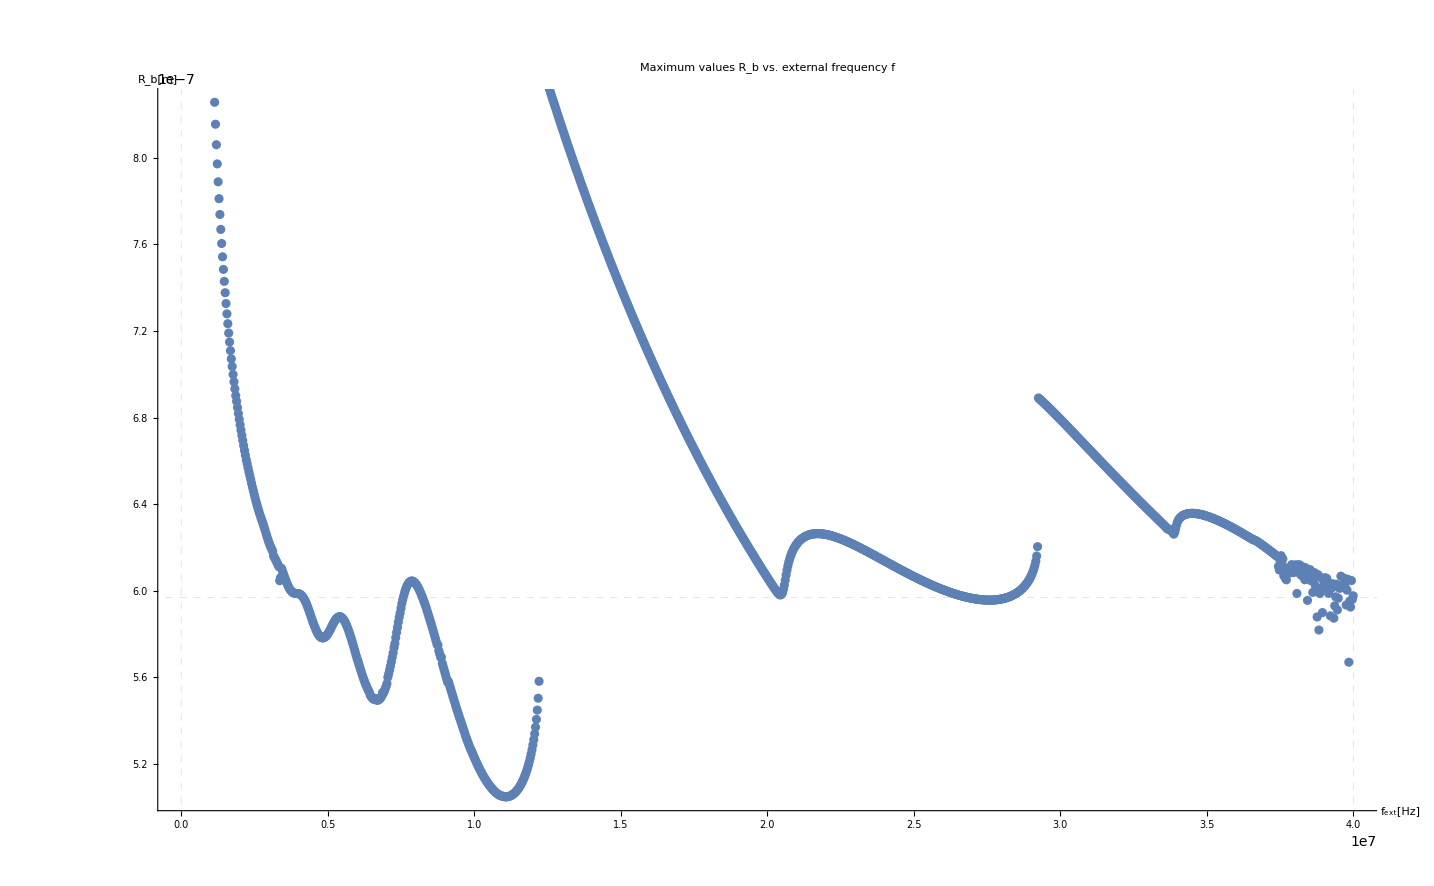

RadiusB= 0.596905 μm

RadiusC= 1.26903 μm

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Radius in final point= 1.4987 μm

1.    =initial frequency [kHz]

40000.    =final frequency [kHz]

30.    =step of frequency [kHz]

1334.3    =Amount of periods [points on X-axis] of the external driving force

Driving frequency fconf= kHz

Номер периода вынуждающей силы считается с 110 по 120

Всего периодов 11

{1684.5,Null}

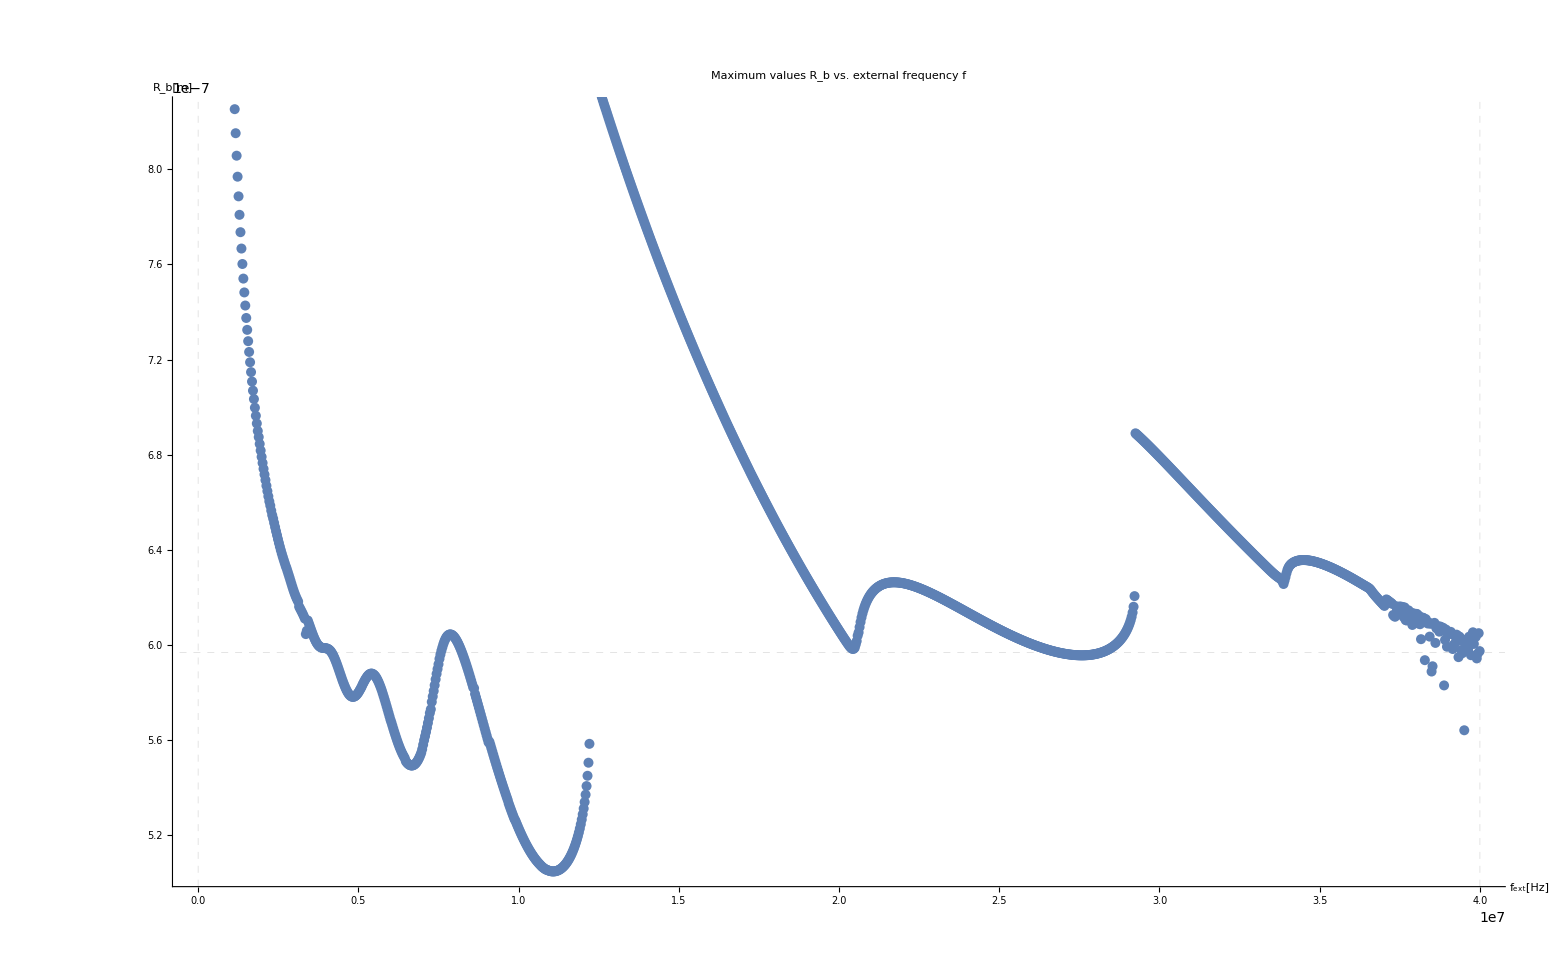

RadiusB= 0.596905 μm

RadiusC= 1.26903 μm

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Radius in final point= 1.4987 μm

```mathematica
2220.5/60
```

```mathematica
Reqright6[Rl0,Rb0,(1+Ampl)*pl1]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

1.4987×10^-6

```mathematica
(*\Max Rb for bifurcation*)
```

1.    =initial frequency [kHz]

60000.    =final frequency [kHz]

100.    =step of frequency [kHz]

600.99    =Amount of periods [points on X-axis] of the external driving force

Driving frequency fconf= 100 kHz

Номер периода вынуждающей силы считается с 40 по 46

Всего периодов 7

{406.749,Null}

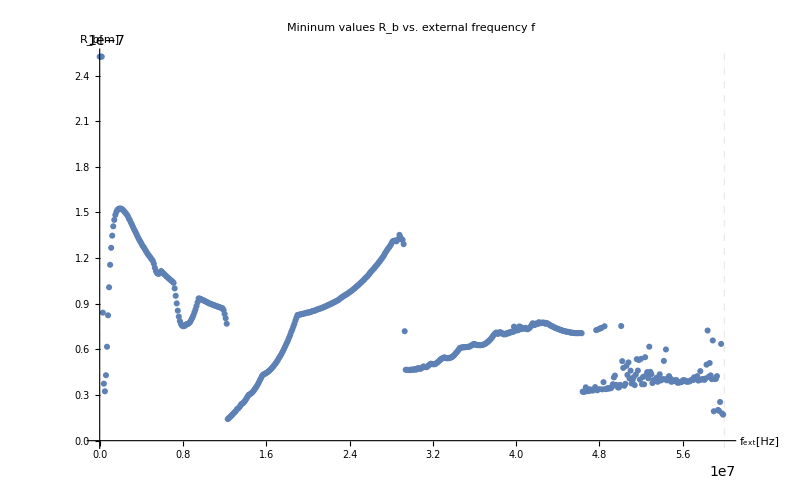

```mathematica
(*Min Rb for bifurcation*)
fconf=1*10^5;(*Hz*)
freq1=0.01;
freq2=600;
stepfreq=1;
numperiodsinit=k1;
numperiodsfin=k2 ;

Text[1.0freq1*fconf*10^-3"   =initial frequency [kHz]"]
Text[1.0freq2*fconf*10^-3"   =final frequency [kHz]"]
Text[1.0stepfreq*fconf*10^-3"   =step of frequency [kHz]"]
Text[(freq2-freq1+stepfreq)/(1.0stepfreq)"   =Amount of periods [points on X-axis] of the external driving force"]
StringJoin["Driving frequency fconf= ",ToString[fconf*10^-3 "kHz"]]
StringJoin["Номер периода вынуждающей силы считается с ",ToString[k1], " по ", ToString[k2]]
StringJoin["Всего периодов ",ToString[k2-k1+1]]


(*M=Table[{i,10^0*(Rb[i][j/i]/.ndsmod)},{j,numperiodsinit,numperiodsfin},{i,freq1*fconf,freq2*fconf,stepfreq*fconf}]*)


AbsoluteTiming[Minim=Table[{i,Min[(Rb[i]/.ndsmod)["ValuesOnGrid"]]},(*{j,numperiodsinit,numperiodsfin},*){i,freq1*fconf,freq2*fconf,stepfreq*fconf}];]

(*MatrixForm[M,
TableHeadings->{
{
Column[Table[StringJoin["n-th number of period of ext driv force n=",ToString[k]],{k,m1,m2}]]

(*StringJoin["n-th number of period of ext driv force n=",ToString[m1]],
StringJoin["n-th number of period of ext driv force n=",ToString[m1+1]]*)
},
{

StringJoin["Ext freq[kHz]=",ToString[k1*fconf*10^-3]],
StringJoin["Ext freq[kHz]=",ToString[(k1+1)*fconf*10^-3]]
}
}
]*)


ListPlot[Minim,
PlotLabel->"Mininum values R_b vs. external frequency f",
AxesLabel->{"f_ext[Hz]","R_b[m]"},
LabelStyle->Directive[Black,12],
(*PlotStyle->{Black(*,PointSize[0.05/6]*)}*)
(*Frame->True,
FrameLabel->{"f_ext[MHz]","R_b[μm]"},*)
GridLines->{{freq1*fconf,freq2*fconf}
,{ RadiusB ,
RadiusC}},
GridLinesStyle->Directive[Dashed]
]
(*\Min Rb for bifurcation*)
```

```mathematica
200/0.3
0.1*fconf
```

666.667

10000.

```mathematica
freq2*fconf*1.0*10^-6
```

0.28

```mathematica
x0=1000*10^3;
stepf=200*10^3;
xfunc[n_]:=(n-1)*stepf+x0;
xfunc[70]
```

14800000

```mathematica
kc=1.0*10^-6;
xfunc[10]*kc
xfunc[33]*kc
xfunc[58]*kc
xfunc[87]*kc
xfunc[133]*kc
xfunc[167]*kc
xfunc[179]*kc
xfunc[202]*kc
xfunc[233]*kc
xfunc[237]*kc
```

2.8

7.4

12.4

18.2

27.4

34.2

36.6

41.2

47.4

48.2

1000    =initial frequency [kHz]

50000    =final frequency [kHz]

200.    =step of frequency [kHz]

246.    =Amount of periods of the external driving force

50    =Расчет начинается с этого номера периода вынуждающей силы

70    =Final number of periods of driving force we finish calculations

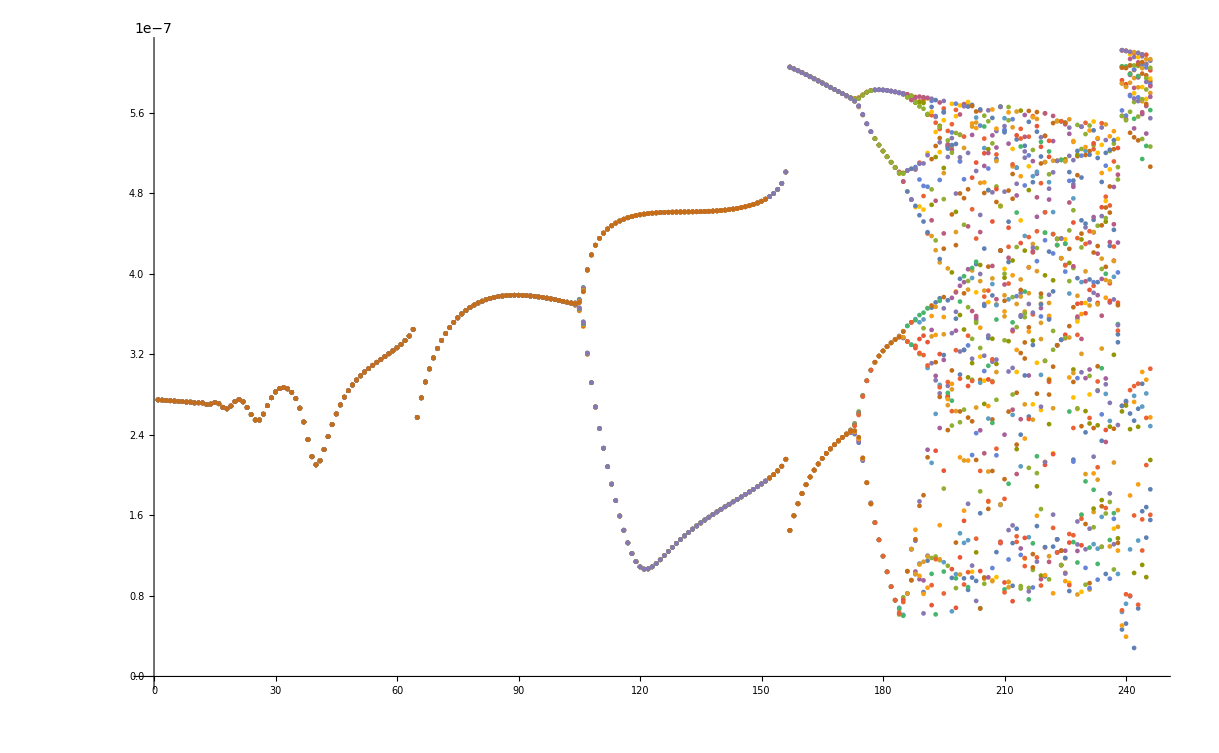

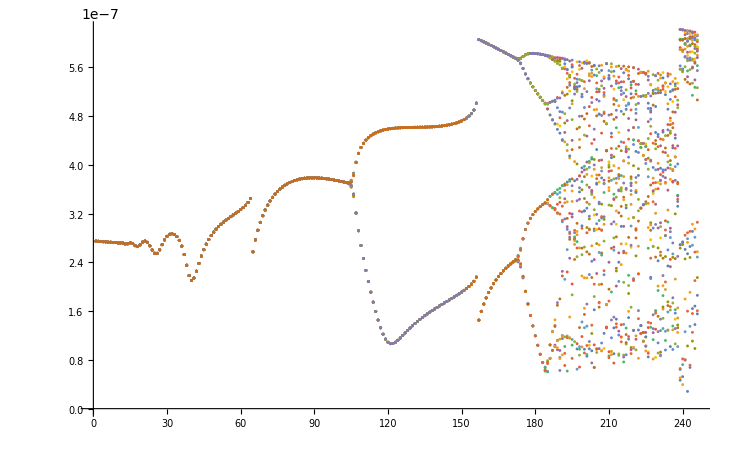
```mathematica
Export["plot.png",-Graphics-,ImageResolution->2500]
```

plot.png

```mathematica
freq1*fconf
freq2*fconf
stepfreq*fconf
```

1000000

50000000

20000000

```mathematica
Export["out.xls",M]
```

out.xls

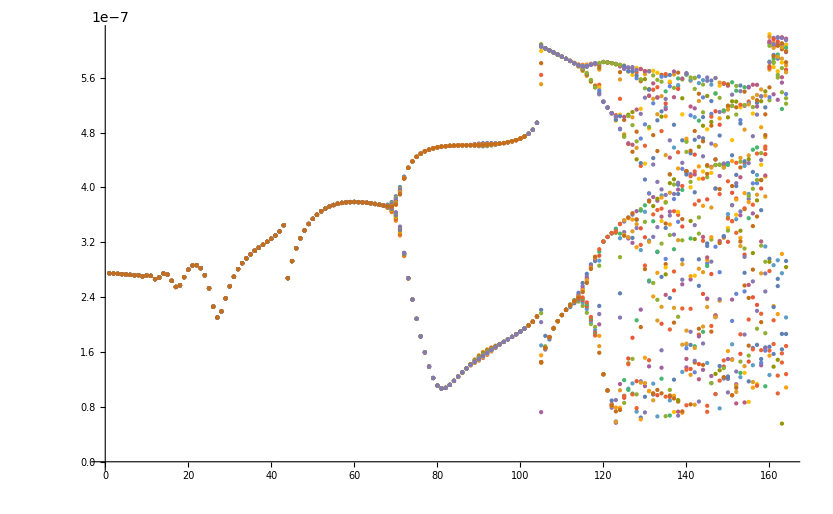

```mathematica
ListPlot[M]
```

```mathematica
Frequency[n_]:=(freq1+(n-1)*stepfreq)*fconf;
Text[Frequency[99]," = External frequency [kHz]"]
```

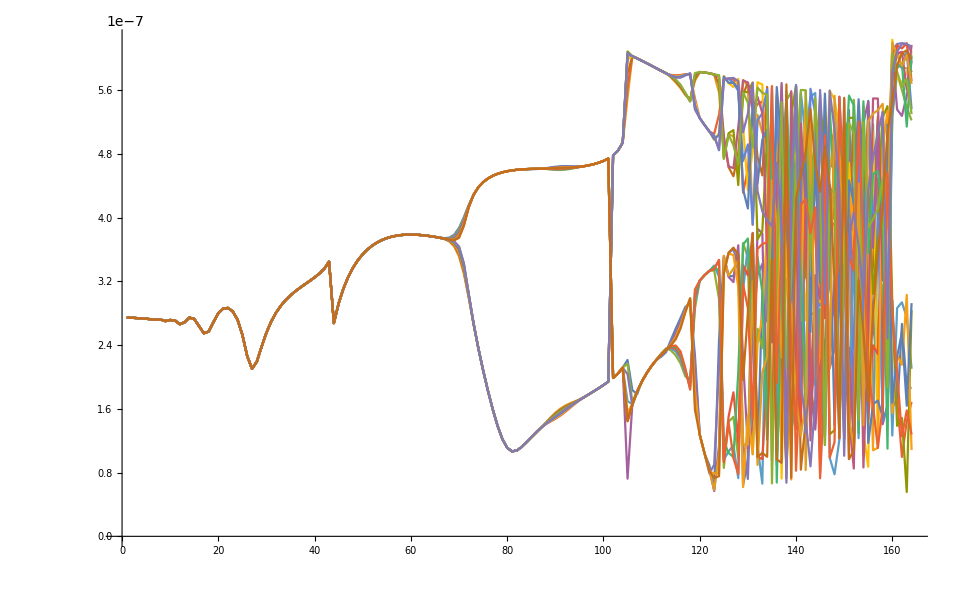

1000    =initial frequency [kHz]

50000    =final frequency [kHz]

300.    =step of frequency [kHz]

166.667    =Amount of periods of the external driving force

20    =Расчет начинается с этого номера периода вынуждающей силы

40    =Final number of periods of driving force we finish calculations

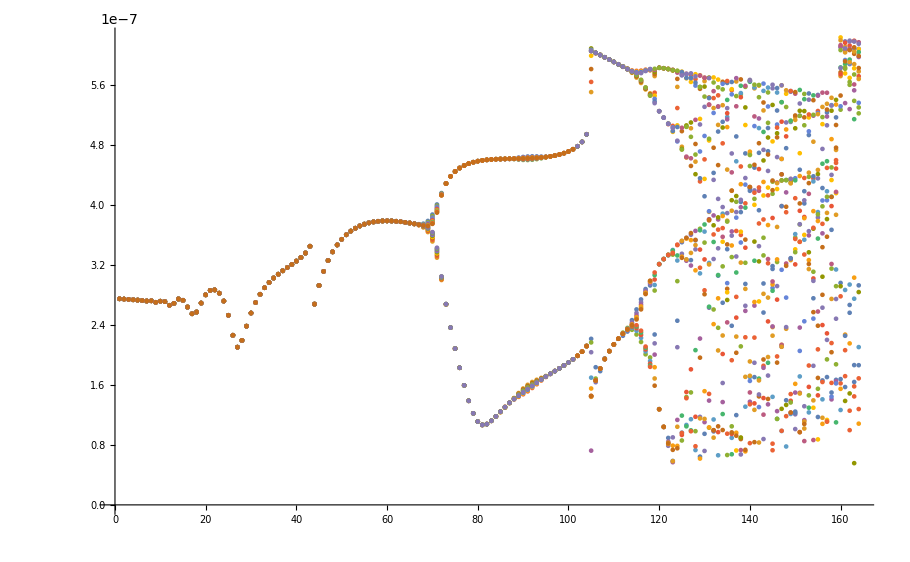

```mathematica
ListLinePlot[M]
```

99.

1000    =initial frequency [kHz]

50000    =final frequency [kHz]

500.    =step of frequency [kHz]

100.    =Amount of periods of the external driving force

10    =Расчет начинается с этого номера периода вынуждающей силы

30    =Final number of periods of driving force we finish calculations

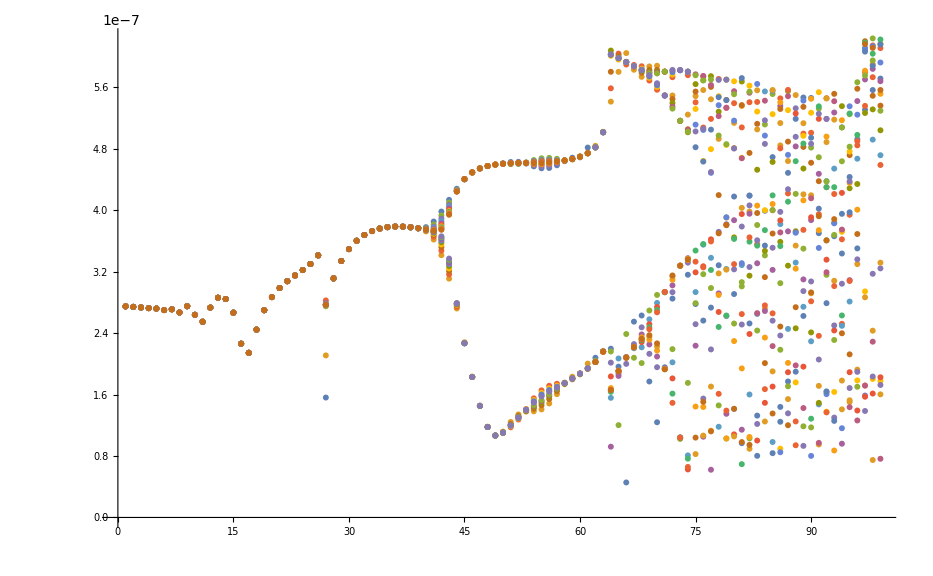

1000    =initial frequency [kHz]

50000    =final frequency [kHz]

500.    =step of frequency [kHz]

100.    =Amount of periods of the external driving force

```mathematica
(50-1+0.5)/0.5
```

```mathematica
"   =Расчет ничинается с этого номера периода вынуждающей силы" m1=5
```

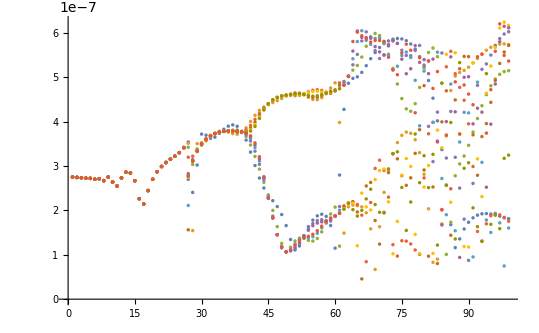

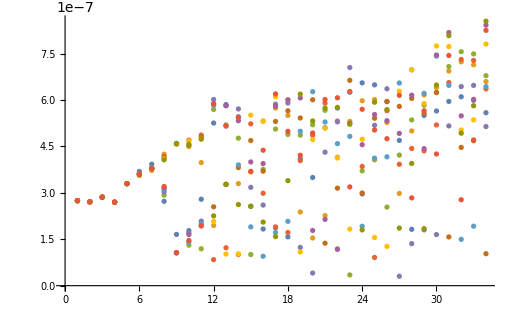

```mathematica
"   =Final number of periods of driving force we finish calculations" m2=15
```

(11.7894 | 12.3478 | 12.8772 | 13.3816 | 13.864 | 14.327 | 14.7726 | 15.2025 | 15.6183 | 16.0211 | 16.4121 | 16.7922 | 17.1623 | 17.523 | 17.875
11.7894 | 12.3478 | 12.8772 | 13.3816 | 13.864 | 14.327 | 14.7726 | 15.2025 | 15.6183 | 16.0211 | 16.4121 | 16.7922 | 17.1623 | 17.523 | 17.875
11.7894 | 12.3478 | 12.8772 | 13.3816 | 13.864 | 14.327 | 14.7726 | 15.2025 | 15.6183 | 16.0211 | 16.4121 | 16.7922 | 17.1623 | 17.523 | 17.875)

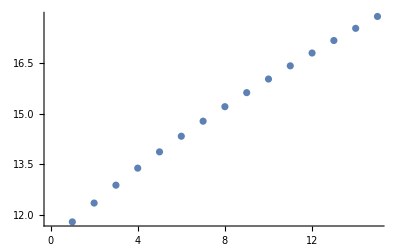

```mathematica
f[x_]:=Log[x]+3x^0.5
M=Table[f[j],{i,1,3},{j,10,24}];
MatrixForm[M]
ListPlot[M[[1]]]
```

```mathematica
Rb[1*fconf][1/(1*fconf)]/.ndsmod
```

2.76046×10^-7

2275    =initial frequency [kHz]

8645    =final frequency [kHz]

91    =step of frequency [kHz]

=From this number of periods of driving force we start calculations

5    =Final number of periods of driving force we finish calculations

91000    =step of frequency

(2.7302×10^-7 | 2.7302×10^-7 | 2.7302×10^-7 | 2.7302×10^-7 | 2.7302×10^-7
2.72793×10^-7 | 2.72793×10^-7 | 2.72793×10^-7 | 2.72793×10^-7 | 2.72793×10^-7
2.7259×10^-7 | 2.7259×10^-7 | 2.7259×10^-7 | 2.7259×10^-7 | 2.7259×10^-7
2.72593×10^-7 | 2.72595×10^-7 | 2.72595×10^-7 | 2.72595×10^-7 | 2.72595×10^-7
2.72561×10^-7 | 2.72562×10^-7 | 2.72562×10^-7 | 2.72562×10^-7 | 2.72562×10^-7
2.72236×10^-7 | 2.72234×10^-7 | 2.72234×10^-7 | 2.72234×10^-7 | 2.72234×10^-7
2.71818×10^-7 | 2.71815×10^-7 | 2.71815×10^-7 | 2.71815×10^-7 | 2.71815×10^-7
2.71708×10^-7 | 2.71709×10^-7 | 2.71709×10^-7 | 2.71709×10^-7 | 2.71709×10^-7
2.71962×10^-7 | 2.71965×10^-7 | 2.71965×10^-7 | 2.71965×10^-7 | 2.71965×10^-7
2.72188×10^-7 | 2.7219×10^-7 | 2.7219×10^-7 | 2.7219×10^-7 | 2.7219×10^-7
2.71964×10^-7 | 2.71962×10^-7 | 2.71962×10^-7 | 2.71962×10^-7 | 2.71962×10^-7
2.71244×10^-7 | 2.71245×10^-7 | 2.71245×10^-7 | 2.71245×10^-7 | 2.71245×10^-7
2.70409×10^-7 | 2.70418×10^-7 | 2.70418×10^-7 | 2.70418×10^-7 | 2.70418×10^-7
2.69979×10^-7 | 2.69988×10^-7 | 2.69988×10^-7 | 2.69988×10^-7 | 2.69988×10^-7
2.70236×10^-7 | 2.70231×10^-7 | 2.70231×10^-7 | 2.70231×10^-7 | 2.70231×10^-7
2.71037×10^-7 | 2.71016×10^-7 | 2.71015×10^-7 | 2.71015×10^-7 | 2.71015×10^-7
2.71917×10^-7 | 2.71888×10^-7 | 2.71888×10^-7 | 2.71888×10^-7 | 2.71888×10^-7
2.72362×10^-7 | 2.72335×10^-7 | 2.72335×10^-7 | 2.72335×10^-7 | 2.72335×10^-7
2.72045×10^-7 | 2.72035×10^-7 | 2.72036×10^-7 | 2.72036×10^-7 | 2.72036×10^-7
2.70933×10^-7 | 2.7097×10^-7 | 2.70969×10^-7 | 2.70969×10^-7 | 2.70969×10^-7
2.69287×10^-7 | 2.6939×10^-7 | 2.69389×10^-7 | 2.69389×10^-7 | 2.69389×10^-7
2.67565×10^-7 | 2.67717×10^-7 | 2.67716×10^-7 | 2.67716×10^-7 | 2.67716×10^-7
2.66282×10^-7 | 2.66425×10^-7 | 2.66424×10^-7 | 2.66424×10^-7 | 2.66424×10^-7
2.6584×10^-7 | 2.65909×10^-7 | 2.6591×10^-7 | 2.6591×10^-7 | 2.6591×10^-7
2.664×10^-7 | 2.66372×10^-7 | 2.66372×10^-7 | 2.66372×10^-7 | 2.66372×10^-7
2.67845×10^-7 | 2.67743×10^-7 | 2.67741×10^-7 | 2.67741×10^-7 | 2.67741×10^-7
2.69836×10^-7 | 2.69698×10^-7 | 2.69696×10^-7 | 2.69696×10^-7 | 2.69696×10^-7
2.7194×10^-7 | 2.71784×10^-7 | 2.71782×10^-7 | 2.71782×10^-7 | 2.71782×10^-7
2.73737×10^-7 | 2.7356×10^-7 | 2.7356×10^-7 | 2.7356×10^-7 | 2.7356×10^-7
2.74897×10^-7 | 2.74703×10^-7 | 2.74705×10^-7 | 2.74705×10^-7 | 2.74705×10^-7
2.75208×10^-7 | 2.75034×10^-7 | 2.75038×10^-7 | 2.75038×10^-7 | 2.75038×10^-7
2.74579×10^-7 | 2.74502×10^-7 | 2.74505×10^-7 | 2.74505×10^-7 | 2.74505×10^-7
2.73026×10^-7 | 2.73143×10^-7 | 2.7314×10^-7 | 2.7314×10^-7 | 2.7314×10^-7
2.70664×10^-7 | 2.71049×10^-7 | 2.71037×10^-7 | 2.71037×10^-7 | 2.71037×10^-7
2.67692×10^-7 | 2.68356×10^-7 | 2.6834×10^-7 | 2.6834×10^-7 | 2.6834×10^-7
2.64378×10^-7 | 2.65246×10^-7 | 2.65236×10^-7 | 2.65236×10^-7 | 2.65236×10^-7
2.61047×10^-7 | 2.61964×10^-7 | 2.61971×10^-7 | 2.61971×10^-7 | 2.61971×10^-7
2.58051×10^-7 | 2.5883×10^-7 | 2.58854×10^-7 | 2.58855×10^-7 | 2.58855×10^-7
2.55728×10^-7 | 2.56225×10^-7 | 2.56252×10^-7 | 2.56254×10^-7 | 2.56254×10^-7
2.54358×10^-7 | 2.54533×10^-7 | 2.5455×10^-7 | 2.54551×10^-7 | 2.54551×10^-7
2.54115×10^-7 | 2.54057×10^-7 | 2.5406×10^-7 | 2.54061×10^-7 | 2.54061×10^-7
2.55036×10^-7 | 2.54924×10^-7 | 2.54924×10^-7 | 2.54924×10^-7 | 2.54924×10^-7
2.57027×10^-7 | 2.57045×10^-7 | 2.57055×10^-7 | 2.57056×10^-7 | 2.57056×10^-7
2.59889×10^-7 | 2.60146×10^-7 | 2.6017×10^-7 | 2.60171×10^-7 | 2.60171×10^-7
2.63364×10^-7 | 2.63858×10^-7 | 2.63885×10^-7 | 2.63886×10^-7 | 2.63886×10^-7
2.6718×10^-7 | 2.67808×10^-7 | 2.67824×10^-7 | 2.67824×10^-7 | 2.67824×10^-7
2.71088×10^-7 | 2.71686×10^-7 | 2.71684×10^-7 | 2.71684×10^-7 | 2.71684×10^-7
2.74873×10^-7 | 2.75269×10^-7 | 2.75255×10^-7 | 2.75255×10^-7 | 2.75255×10^-7
2.78366×10^-7 | 2.78418×10^-7 | 2.78413×10^-7 | 2.78413×10^-7 | 2.78413×10^-7
2.81441×10^-7 | 2.81068×10^-7 | 2.81095×10^-7 | 2.81093×10^-7 | 2.81093×10^-7
2.84009×10^-7 | 2.83198×10^-7 | 2.83277×10^-7 | 2.83269×10^-7 | 2.8327×10^-7
2.86009×10^-7 | 2.84821×10^-7 | 2.84957×10^-7 | 2.84942×10^-7 | 2.84943×10^-7
2.87406×10^-7 | 2.85961×10^-7 | 2.86142×10^-7 | 2.86121×10^-7 | 2.86123×10^-7
2.8818×10^-7 | 2.86645×10^-7 | 2.86846×10^-7 | 2.86821×10^-7 | 2.86824×10^-7
2.88327×10^-7 | 2.86893×10^-7 | 2.87079×10^-7 | 2.87056×10^-7 | 2.87059×10^-7
2.87852×10^-7 | 2.86713×10^-7 | 2.86849×10^-7 | 2.86834×10^-7 | 2.86836×10^-7
2.86766×10^-7 | 2.86094×10^-7 | 2.8616×10^-7 | 2.86154×10^-7 | 2.86154×10^-7
2.8509×10^-7 | 2.85012×10^-7 | 2.85005×10^-7 | 2.85006×10^-7 | 2.85005×10^-7
2.82845×10^-7 | 2.83423×10^-7 | 2.83366×10^-7 | 2.83369×10^-7 | 2.83369×10^-7
2.80061×10^-7 | 2.81273×10^-7 | 2.81209×10^-7 | 2.81209×10^-7 | 2.81209×10^-7
2.7677×10^-7 | 2.785×10^-7 | 2.78482×10^-7 | 2.78478×10^-7 | 2.78478×10^-7
2.73011×10^-7 | 2.75044×10^-7 | 2.75112×10^-7 | 2.7511×10^-7 | 2.7511×10^-7
2.68827×10^-7 | 2.70856×10^-7 | 2.71017×10^-7 | 2.71025×10^-7 | 2.71026×10^-7
2.6427×10^-7 | 2.65908×10^-7 | 2.66112×10^-7 | 2.66135×10^-7 | 2.66138×10^-7
2.59402×10^-7 | 2.60208×10^-7 | 2.6034×10^-7 | 2.60361×10^-7 | 2.60365×10^-7
2.54296×10^-7 | 2.53813×10^-7 | 2.53699×10^-7 | 2.53674×10^-7 | 2.53669×10^-7
2.49038×10^-7 | 2.46848×10^-7 | 2.46285×10^-7 | 2.46145×10^-7 | 2.4611×10^-7
2.43732×10^-7 | 2.39522×10^-7 | 2.38339×10^-7 | 2.38013×10^-7 | 2.37923×10^-7
2.38496×10^-7 | 2.3215×10^-7 | 2.30285×10^-7 | 2.29743×10^-7 | 2.29586×10^-7
2.33471×10^-7 | 2.25158×10^-7 | 2.22738×10^-7 | 2.22039×10^-7 | 2.21836×10^-7
2.2881×10^-7 | 2.19069×10^-7 | 2.16458×10^-7 | 2.15753×10^-7 | 2.15559×10^-7)

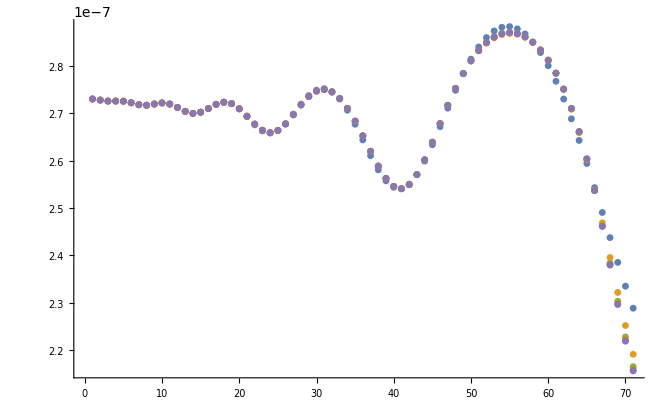

```mathematica
fconf=91000;
(*Number of frequencies*)
k1=25;
k2=95;
Text[k1*fconf*10^-3"   =initial frequency [kHz]"]
Text[k2*fconf*10^-3"   =final frequency [kHz]"]
Text[fconf*10^-3"   =step of frequency [kHz]"]
(*Number of periods since m1 to m2*)
m1=1;
m2=5;
Text[m1"   =From this number of periods of driving force we start calculations"]
Text[m2"   =Final number of periods of driving force we finish calculations"]
Text[fconf"   =step of frequency"]
M=Table[Rb[i*fconf][j/(i*fconf)]/.ndsmod,{i,k1,k2},{j,m1,m2}];
MatrixForm[M]
B=Transpose[M];
ListPlot[B]
```

```mathematica
fconf=10000;
(*Number of frequencies*)
k1=1;
k2=3;
Text[k1*fconf*10^-3"   =initial frequency [kHz]"]
Text[k2*fconf*10^-3"   =final frequency [kHz]"]
Text[fconf*10^-3"   =step of frequency [kHz]"]
(*Number of periods since m1 to m2*)
m1=1;
m2=4;
Text[m1  "   =From this number of periods of driving force we start calculations"]
Text[m2  "   =Final number of periods of driving force we finish calculations"]
Text[fconf"   =step of frequency"]
M=Table[Rb[i*fconf][j/(i*fconf)]/.ndsmod,{i,k1,k2},{j,m1,m2}];
MatrixForm[M]
(*B=Transpose[M];
ListPlot[B]*)
```

10    =initial frequency [kHz]

30    =final frequency [kHz]

10    =step of frequency [kHz]

=From this number of periods of driving force we start calculations

4    =Final number of periods of driving force we finish calculations

10000    =step of frequency

(2.76141×10^-7 | 2.76141×10^-7 | 2.76141×10^-7 | 2.76141×10^-7
2.76129×10^-7 | 2.76129×10^-7 | 2.76129×10^-7 | 2.76129×10^-7
2.76118×10^-7 | 2.76118×10^-7 | 2.76118×10^-7 | 2.76118×10^-7)

```mathematica
freq1=1;
freq2=90;
stepfreq=0.5;
freq2-freq1+1
(freq2-freq1+1)/stepfreq
```

100

200.

( | Ext freq[kHz]=1000 | Ext freq[kHz]=1500. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
n-th period n=5
n-th period n=6
n-th period n=7
n-th period n=8
n-th period n=9
n-th period n=10
n-th period n=11
n-th period n=12
n-th period n=13
n-th period n=14
n-th period n=15 | 2.74867×10^-7 | 2.74149×10^-7 | 2.73412×10^-7 | 2.72573×10^-7 | 2.71954×10^-7 | 2.70015×10^-7 | 2.7103×10^-7 | 2.66891×10^-7 | 2.75042×10^-7 | 2.63804×10^-7 | 2.54826×10^-7 | 2.73259×10^-7 | 2.8605×10^-7 | 2.84383×10^-7 | 2.66602×10^-7 | 2.26316×10^-7 | 2.14317×10^-7 | 2.44514×10^-7 | 2.69832×10^-7 | 2.86748×10^-7 | 2.98919×10^-7 | 3.08236×10^-7 | 3.15421×10^-7 | 3.22117×10^-7 | 3.29939×10^-7 | 3.41597×10^-7 | 3.53907×10^-7 | 2.40421×10^-7 | 3.02043×10^-7 | 3.71758×10^-7 | 3.6924×10^-7 | 3.62157×10^-7 | 3.64785×10^-7 | 3.73384×10^-7 | 3.82632×10^-7 | 3.89615×10^-7 | 3.92495×10^-7 | 3.89305×10^-7 | 3.78148×10^-7 | 3.58275×10^-7 | 3.31199×10^-7 | 3.00938×10^-7 | 2.72729×10^-7 | 2.5043×10^-7 | 2.34412×10^-7 | 2.21801×10^-7 | 2.08445×10^-7 | 1.90577×10^-7 | 1.65656×10^-7 | 1.34398×10^-7 | 1.10854×10^-7 | 1.19771×10^-7 | 1.43219×10^-7 | 1.63352×10^-7 | 1.78012×10^-7 | 1.87588×10^-7 | 1.91302×10^-7 | 1.86446×10^-7 | 1.65748×10^-7 | 1.14897×10^-7 | 2.79473×10^-7 | 4.27389×10^-7 | 4.86159×10^-7 | 4.97193×10^-7 | 5.0067×10^-7 | 5.10716×10^-7 | 5.25767×10^-7 | 5.41555×10^-7 | 5.55521×10^-7 | 5.66804×10^-7 | 5.75404×10^-7 | 5.81562×10^-7 | 5.85443×10^-7 | 5.87024×10^-7 | 5.86071×10^-7 | 5.82156×10^-7 | 5.7469×10^-7 | 5.62944×10^-7 | 5.46047×10^-7 | 5.22955×10^-7 | 4.92368×10^-7 | 4.52618×10^-7 | 4.01576×10^-7 | 3.3684×10^-7 | 2.5704×10^-7 | 1.67771×10^-7 | 1.15984×10^-7 | 1.35769×10^-7 | 1.58012×10^-7 | 1.73186×10^-7 | 1.83158×10^-7 | 1.89194×10^-7 | 1.92147×10^-7 | 1.92743×10^-7 | 1.91669×10^-7 | 1.89558×10^-7 | 1.86933×10^-7 | 1.84131×10^-7 | 1.81231×10^-7
 | 2.74867×10^-7 | 2.74149×10^-7 | 2.73412×10^-7 | 2.72573×10^-7 | 2.71954×10^-7 | 2.70015×10^-7 | 2.7103×10^-7 | 2.66891×10^-7 | 2.75042×10^-7 | 2.63804×10^-7 | 2.54826×10^-7 | 2.73259×10^-7 | 2.86049×10^-7 | 2.84383×10^-7 | 2.66602×10^-7 | 2.26263×10^-7 | 2.14322×10^-7 | 2.44515×10^-7 | 2.69897×10^-7 | 2.86978×10^-7 | 2.98659×10^-7 | 3.07357×10^-7 | 3.14936×10^-7 | 3.22124×10^-7 | 3.29941×10^-7 | 3.41378×10^-7 | 3.51167×10^-7 | 1.544×10^-7 | 3.50315×10^-7 | 3.52428×10^-7 | 3.56143×10^-7 | 3.65183×10^-7 | 3.73385×10^-7 | 3.77999×10^-7 | 3.78657×10^-7 | 3.76279×10^-7 | 3.72814×10^-7 | 3.71408×10^-7 | 3.75405×10^-7 | 3.85862×10^-7 | 4.00181×10^-7 | 4.14149×10^-7 | 4.25107×10^-7 | 4.328×10^-7 | 4.38235×10^-7 | 4.42626×10^-7 | 4.46992×10^-7 | 4.51921×10^-7 | 4.57283×10^-7 | 4.62113×10^-7 | 4.64894×10^-7 | 4.64314×10^-7 | 4.60273×10^-7 | 4.54458×10^-7 | 4.49863×10^-7 | 4.49312×10^-7 | 4.53829×10^-7 | 4.62638×10^-7 | 4.7569×10^-7 | 4.8712×10^-7 | 3.97892×10^-7 | 1.48889×10^-7 | 2.07908×10^-7 | 2.1185×10^-7 | 2.1069×10^-7 | 2.07811×10^-7 | 1.94466×10^-7 | 1.5835×10^-7 | 6.69708×10^-8 | 1.63064×10^-7 | 2.40545×10^-7 | 2.91142×10^-7 | 3.27103×10^-7 | 3.52544×10^-7 | 3.68885×10^-7 | 3.76169×10^-7 | 3.73497×10^-7 | 3.59093×10^-7 | 3.30021×10^-7 | 2.81289×10^-7 | 2.03411×10^-7 | 8.30011×10^-8 | 9.00171×10^-8 | 1.69558×10^-7 | 3.67587×10^-7 | 4.69777×10^-7 | 5.02274×10^-7 | 5.10559×10^-7 | 5.15318×10^-7 | 5.22417×10^-7 | 5.31856×10^-7 | 5.42187×10^-7 | 5.52065×10^-7 | 5.60582×10^-7 | 5.67245×10^-7 | 5.71852×10^-7 | 5.74379×10^-7 | 5.74874×10^-7 | 5.73406×10^-7
 | 2.74867×10^-7 | 2.74149×10^-7 | 2.73412×10^-7 | 2.72573×10^-7 | 2.71954×10^-7 | 2.70015×10^-7 | 2.7103×10^-7 | 2.66891×10^-7 | 2.75042×10^-7 | 2.63804×10^-7 | 2.54826×10^-7 | 2.73259×10^-7 | 2.86049×10^-7 | 2.84383×10^-7 | 2.66602×10^-7 | 2.26247×10^-7 | 2.14322×10^-7 | 2.44515×10^-7 | 2.69882×10^-7 | 2.86889×10^-7 | 2.98781×10^-7 | 3.07777×10^-7 | 3.15128×10^-7 | 3.22122×10^-7 | 3.29937×10^-7 | 3.41281×10^-7 | 3.42141×10^-7 | 3.03232×10^-7 | 3.38307×10^-7 | 3.46712×10^-7 | 3.59703×10^-7 | 3.68955×10^-7 | 3.7362×10^-7 | 3.75707×10^-7 | 3.7716×10^-7 | 3.78926×10^-7 | 3.80777×10^-7 | 3.81148×10^-7 | 3.77311×10^-7 | 3.66369×10^-7 | 3.47119×10^-7 | 3.2141×10^-7 | 2.92692×10^-7 | 2.63103×10^-7 | 2.32618×10^-7 | 1.99885×10^-7 | 1.63344×10^-7 | 1.25471×10^-7 | 1.05963×10^-7 | 1.16775×10^-7 | 1.30954×10^-7 | 1.37458×10^-7 | 1.36679×10^-7 | 1.3249×10^-7 | 1.30797×10^-7 | 1.36722×10^-7 | 1.51566×10^-7 | 1.71013×10^-7 | 1.91791×10^-7 | 2.07306×10^-7 | 1.1942×10^-7 | 4.90357×10^-7 | 5.01323×10^-7 | 5.158×10^-7 | 5.26368×10^-7 | 5.45168×10^-7 | 5.69603×10^-7 | 5.89819×10^-7 | 5.9836×10^-7 | 5.93607×10^-7 | 5.77228×10^-7 | 5.51696×10^-7 | 5.19671×10^-7 | 4.84601×10^-7 | 4.51731×10^-7 | 4.28522×10^-7 | 4.23117×10^-7 | 4.40263×10^-7 | 4.76806×10^-7 | 5.20804×10^-7 | 5.55573×10^-7 | 5.65632×10^-7 | 5.46095×10^-7 | 4.86515×10^-7 | 1.00797×10^-7 | 1.73302×10^-7 | 2.77814×10^-7 | 3.04583×10^-7 | 3.22329×10^-7 | 3.46504×10^-7 | 3.76111×10^-7 | 4.06923×10^-7 | 4.35645×10^-7 | 4.60434×10^-7 | 4.80519×10^-7 | 4.95758×10^-7 | 5.06321×10^-7 | 5.12482×10^-7 | 5.14511×10^-7
 | 2.74867×10^-7 | 2.74149×10^-7 | 2.73412×10^-7 | 2.72573×10^-7 | 2.71954×10^-7 | 2.70015×10^-7 | 2.7103×10^-7 | 2.66891×10^-7 | 2.75042×10^-7 | 2.63804×10^-7 | 2.54826×10^-7 | 2.73259×10^-7 | 2.86049×10^-7 | 2.84383×10^-7 | 2.66602×10^-7 | 2.26243×10^-7 | 2.14322×10^-7 | 2.44515×10^-7 | 2.69886×10^-7 | 2.86924×10^-7 | 2.98724×10^-7 | 3.07576×10^-7 | 3.15052×10^-7 | 3.22122×10^-7 | 3.29937×10^-7 | 3.41239×10^-7 | 3.19711×10^-7 | 3.21887×10^-7 | 3.32356×10^-7 | 3.49124×10^-7 | 3.60765×10^-7 | 3.67798×10^-7 | 3.72589×10^-7 | 3.76122×10^-7 | 3.7835×10^-7 | 3.78956×10^-7 | 3.77923×10^-7 | 3.76171×10^-7 | 3.76082×10^-7 | 3.80752×10^-7 | 3.91241×10^-7 | 4.04926×10^-7 | 4.18282×10^-7 | 4.29759×10^-7 | 4.39349×10^-7 | 4.47327×10^-7 | 4.53677×10^-7 | 4.57935×10^-7 | 4.59557×10^-7 | 4.58957×10^-7 | 4.58077×10^-7 | 4.5914×10^-7 | 4.62641×10^-7 | 4.67035×10^-7 | 4.70423×10^-7 | 4.71738×10^-7 | 4.70205×10^-7 | 4.66159×10^-7 | 4.63333×10^-7 | 4.71591×10^-7 | 4.87068×10^-7 | 2.10297×10^-7 | 2.15893×10^-7 | 2.18833×10^-7 | 2.13163×10^-7 | 1.89081×10^-7 | 8.42562×10^-8 | 2.17657×10^-7 | 2.94489×10^-7 | 3.12857×10^-7 | 2.89906×10^-7 | 2.29778×10^-7 | 1.22627×10^-7 | 9.69785×10^-8 | 1.31543×10^-7 | 1.30691×10^-7 | 1.24408×10^-7 | 1.10696×10^-7 | 1.00729×10^-7 | 2.73063×10^-7 | 3.72366×10^-7 | 3.98139×10^-7 | 3.53941×10^-7 | 2.01894×10^-7 | 5.23317×10^-7 | 5.58026×10^-7 | 5.07688×10^-7 | 4.76999×10^-7 | 4.47935×10^-7 | 3.949×10^-7 | 2.98784×10^-7 | 1.52444×10^-7 | 1.31064×10^-7 | 1.69738×10^-7 | 1.87848×10^-7 | 1.93128×10^-7 | 1.90023×10^-7 | 1.82814×10^-7 | 1.75437×10^-7
 | 2.74867×10^-7 | 2.74149×10^-7 | 2.73412×10^-7 | 2.72573×10^-7 | 2.71954×10^-7 | 2.70015×10^-7 | 2.7103×10^-7 | 2.66891×10^-7 | 2.75042×10^-7 | 2.63804×10^-7 | 2.54826×10^-7 | 2.73259×10^-7 | 2.86049×10^-7 | 2.84383×10^-7 | 2.66602×10^-7 | 2.26242×10^-7 | 2.14322×10^-7 | 2.44515×10^-7 | 2.69885×10^-7 | 2.86911×10^-7 | 2.98751×10^-7 | 3.07672×10^-7 | 3.15082×10^-7 | 3.22122×10^-7 | 3.29937×10^-7 | 3.41221×10^-7 | 2.69629×10^-7 | 3.14285×10^-7 | 3.33281×10^-7 | 3.49722×10^-7 | 3.60236×10^-7 | 3.67636×10^-7 | 3.72889×10^-7 | 3.76214×10^-7 | 3.77938×10^-7 | 3.78637×10^-7 | 3.78896×10^-7 | 3.78739×10^-7 | 3.76862×10^-7 | 3.70392×10^-7 | 3.56185×10^-7 | 3.3333×10^-7 | 3.03556×10^-7 | 2.68711×10^-7 | 2.29547×10^-7 | 1.86963×10^-7 | 1.45058×10^-7 | 1.15405×10^-7 | 1.06679×10^-7 | 1.08478×10^-7 | 1.13728×10^-7 | 1.24892×10^-7 | 1.41993×10^-7 | 1.58482×10^-7 | 1.70238×10^-7 | 1.76961×10^-7 | 1.78825×10^-7 | 1.76868×10^-7 | 1.75869×10^-7 | 1.87912×10^-7 | 2.08711×10^-7 | 4.89103×10^-7 | 5.02184×10^-7 | 5.27719×10^-7 | 5.51198×10^-7 | 5.81462×10^-7 | 6.02006×10^-7 | 5.90545×10^-7 | 5.59711×10^-7 | 5.41892×10^-7 | 5.50096×10^-7 | 5.70247×10^-7 | 5.81802×10^-7 | 5.76006×10^-7 | 5.60529×10^-7 | 5.48896×10^-7 | 5.48154×10^-7 | 5.60152×10^-7 | 5.71396×10^-7 | 5.27146×10^-7 | 3.89096×10^-7 | 3.09817×10^-7 | 4.21234×10^-7 | 5.54328×10^-7 | 3.17853×10^-7 | 4.22707×10^-7 | 3.19534×10^-7 | 2.50142×10^-7 | 1.80157×10^-7 | 8.73481×10^-8 | 2.60618×10^-7 | 4.81475×10^-7 | 5.17588×10^-7 | 5.29794×10^-7 | 5.49681×10^-7 | 5.70517×10^-7 | 5.86763×10^-7 | 5.97069×10^-7 | 6.02205×10^-7
 | 2.74867×10^-7 | 2.74149×10^-7 | 2.73412×10^-7 | 2.72573×10^-7 | 2.71954×10^-7 | 2.70015×10^-7 | 2.7103×10^-7 | 2.66891×10^-7 | 2.75042×10^-7 | 2.63804×10^-7 | 2.54826×10^-7 | 2.73259×10^-7 | 2.86049×10^-7 | 2.84383×10^-7 | 2.66602×10^-7 | 2.26241×10^-7 | 2.14322×10^-7 | 2.44515×10^-7 | 2.69885×10^-7 | 2.86916×10^-7 | 2.98738×10^-7 | 3.07626×10^-7 | 3.1507×10^-7 | 3.22122×10^-7 | 3.29937×10^-7 | 3.41213×10^-7 | 1.56136×10^-7 | 3.10729×10^-7 | 3.34037×10^-7 | 3.49438×10^-7 | 3.60184×10^-7 | 3.67802×10^-7 | 3.7291×10^-7 | 3.7613×10^-7 | 3.78005×10^-7 | 3.78817×10^-7 | 3.78588×10^-7 | 3.77433×10^-7 | 3.76371×10^-7 | 3.78006×10^-7 | 3.85314×10^-7 | 3.98274×10^-7 | 4.1355×10^-7 | 4.27999×10^-7 | 4.40015×10^-7 | 4.48877×10^-7 | 4.54473×10^-7 | 4.57506×10^-7 | 4.59407×10^-7 | 4.61242×10^-7 | 4.62808×10^-7 | 4.62992×10^-7 | 4.60792×10^-7 | 4.57111×10^-7 | 4.54607×10^-7 | 4.55023×10^-7 | 4.58523×10^-7 | 4.63872×10^-7 | 4.68408×10^-7 | 4.68837×10^-7 | 4.81592×10^-7 | 2.0794×10^-7 | 2.16322×10^-7 | 2.19734×10^-7 | 1.96353×10^-7 | 4.55901×10^-8 | 2.54952×10^-7 | 2.62962×10^-7 | 1.77014×10^-7 | 1.23957×10^-7 | 1.95518×10^-7 | 2.84965×10^-7 | 3.2771×10^-7 | 3.15999×10^-7 | 2.7787×10^-7 | 2.56309×10^-7 | 2.73219×10^-7 | 3.28372×10^-7 | 3.81676×10^-7 | 2.90875×10^-7 | 9.67141×10^-8 | 2.52584×10^-7 | 8.02417×10^-8 | 3.99268×10^-7 | 4.69191×10^-7 | 1.43933×10^-7 | 4.48672×10^-7 | 5.18953×10^-7 | 5.46744×10^-7 | 5.46202×10^-7 | 3.70132×10^-7 | 2.79007×10^-7 | 3.66152×10^-7 | 3.95303×10^-7 | 4.43292×10^-7 | 4.92425×10^-7 | 5.30837×10^-7 | 5.56508×10^-7 | 5.71429×10^-7
 | 2.74867×10^-7 | 2.74149×10^-7 | 2.73412×10^-7 | 2.72573×10^-7 | 2.71954×10^-7 | 2.70015×10^-7 | 2.7103×10^-7 | 2.66891×10^-7 | 2.75042×10^-7 | 2.63804×10^-7 | 2.54826×10^-7 | 2.73259×10^-7 | 2.86049×10^-7 | 2.84383×10^-7 | 2.66602×10^-7 | 2.26241×10^-7 | 2.14322×10^-7 | 2.44515×10^-7 | 2.69885×10^-7 | 2.86914×10^-7 | 2.98744×10^-7 | 3.07648×10^-7 | 3.15075×10^-7 | 3.22122×10^-7 | 3.29937×10^-7 | 3.4121×10^-7 | 2.10984×10^-7 | 3.10902×10^-7 | 3.33999×10^-7 | 3.49378×10^-7 | 3.6025×10^-7 | 3.67783×10^-7 | 3.7287×10^-7 | 3.76153×10^-7 | 3.78019×10^-7 | 3.7875×10^-7 | 3.78678×10^-7 | 3.78099×10^-7 | 3.7668×10^-7 | 3.72485×10^-7 | 3.61838×10^-7 | 3.41465×10^-7 | 3.10935×10^-7 | 2.72106×10^-7 | 2.28027×10^-7 | 1.83484×10^-7 | 1.45001×10^-7 | 1.1822×10^-7 | 1.06671×10^-7 | 1.11757×10^-7 | 1.2434×10^-7 | 1.34116×10^-7 | 1.3783×10^-7 | 1.38167×10^-7 | 1.40693×10^-7 | 1.48416×10^-7 | 1.60519×10^-7 | 1.73478×10^-7 | 1.83192×10^-7 | 1.86198×10^-7 | 2.00316×10^-7 | 4.83864×10^-7 | 5.02051×10^-7 | 5.41375×10^-7 | 5.8017×10^-7 | 6.04592×10^-7 | 5.82912×10^-7 | 5.73705×10^-7 | 5.87242×10^-7 | 5.88111×10^-7 | 5.8028×10^-7 | 5.49434×10^-7 | 5.16176×10^-7 | 5.24511×10^-7 | 5.48582×10^-7 | 5.56483×10^-7 | 5.44449×10^-7 | 4.92925×10^-7 | 3.90463×10^-7 | 5.13697×10^-7 | 5.35791×10^-7 | 3.98249×10^-7 | 5.56178×10^-7 | 2.71687×10^-7 | 1.9019×10^-7 | 4.84392×10^-7 | 1.54086×10^-7 | 3.53925×10^-7 | 4.20704×10^-7 | 4.19505×10^-7 | 9.50388×10^-8 | 4.88712×10^-7 | 3.08144×10^-7 | 1.78241×10^-7 | 1.50287×10^-7 | 1.92473×10^-7 | 1.71817×10^-7 | 7.48035×10^-8 | 1.60289×10^-7
 | 2.74867×10^-7 | 2.74149×10^-7 | 2.73412×10^-7 | 2.72573×10^-7 | 2.71954×10^-7 | 2.70015×10^-7 | 2.7103×10^-7 | 2.66891×10^-7 | 2.75042×10^-7 | 2.63804×10^-7 | 2.54826×10^-7 | 2.73259×10^-7 | 2.86049×10^-7 | 2.84383×10^-7 | 2.66602×10^-7 | 2.26241×10^-7 | 2.14322×10^-7 | 2.44515×10^-7 | 2.69885×10^-7 | 2.86914×10^-7 | 2.98741×10^-7 | 3.07638×10^-7 | 3.15073×10^-7 | 3.22122×10^-7 | 3.29937×10^-7 | 3.41209×10^-7 | 2.74914×10^-7 | 3.11343×10^-7 | 3.3391×10^-7 | 3.49411×10^-7 | 3.60247×10^-7 | 3.67769×10^-7 | 3.7288×10^-7 | 3.76153×10^-7 | 3.78005×10^-7 | 3.78768×10^-7 | 3.78654×10^-7 | 3.77761×10^-7 | 3.76486×10^-7 | 3.7653×10^-7 | 3.813×10^-7 | 3.93152×10^-7 | 4.09924×10^-7 | 4.26851×10^-7 | 4.4032×10^-7 | 4.4919×10^-7 | 4.54395×10^-7 | 4.57521×10^-7 | 4.59426×10^-7 | 4.60135×10^-7 | 4.59971×10^-7 | 4.60255×10^-7 | 4.62257×10^-7 | 4.65327×10^-7 | 4.6763×10^-7 | 4.68186×10^-7 | 4.6693×10^-7 | 4.65284×10^-7 | 4.66017×10^-7 | 4.69997×10^-7 | 4.73757×10^-7 | 2.03822×10^-7 | 2.1625×10^-7 | 2.16102×10^-7 | 1.20206×10^-7 | 2.38828×10^-7 | 2.07937×10^-7 | 2.00998×10^-7 | 2.69448×10^-7 | 2.89722×10^-7 | 2.93062×10^-7 | 2.19149×10^-7 | 1.02263×10^-7 | 1.75169×10^-7 | 2.78995×10^-7 | 3.16721×10^-7 | 2.987×10^-7 | 1.45887×10^-7 | 1.02715×10^-7 | 2.52479×10^-7 | 3.0086×10^-7 | 1.02971×10^-7 | 3.80731×10^-7 | 3.41165×10^-7 | 5.51322×10^-7 | 2.18326×10^-7 | 5.54861×10^-7 | 3.72799×10^-7 | 1.1867×10^-7 | 1.17273×10^-7 | 5.32409×10^-7 | 3.15876×10^-7 | 2.31081×10^-7 | 4.63744×10^-7 | 5.25011×10^-7 | 5.66657×10^-7 | 6.10732×10^-7 | 6.23748×10^-7 | 6.16742×10^-7
 | 2.74867×10^-7 | 2.74149×10^-7 | 2.73412×10^-7 | 2.72573×10^-7 | 2.71954×10^-7 | 2.70015×10^-7 | 2.7103×10^-7 | 2.66891×10^-7 | 2.75042×10^-7 | 2.63804×10^-7 | 2.54826×10^-7 | 2.73259×10^-7 | 2.86049×10^-7 | 2.84383×10^-7 | 2.66602×10^-7 | 2.26241×10^-7 | 2.14322×10^-7 | 2.44515×10^-7 | 2.69885×10^-7 | 2.86914×10^-7 | 2.98743×10^-7 | 3.07643×10^-7 | 3.15073×10^-7 | 3.22122×10^-7 | 3.29937×10^-7 | 3.41208×10^-7 | 2.82589×10^-7 | 3.11413×10^-7 | 3.33907×10^-7 | 3.49417×10^-7 | 3.6024×10^-7 | 3.67774×10^-7 | 3.72882×10^-7 | 3.76151×10^-7 | 3.7801×10^-7 | 3.78766×10^-7 | 3.7866×10^-7 | 3.77933×10^-7 | 3.76608×10^-7 | 3.73587×10^-7 | 3.65496×10^-7 | 3.4742×10^-7 | 3.16425×10^-7 | 2.74316×10^-7 | 2.27342×10^-7 | 1.82915×10^-7 | 1.45322×10^-7 | 1.17703×10^-7 | 1.06658×10^-7 | 1.09823×10^-7 | 1.1742×10^-7 | 1.27481×10^-7 | 1.41131×10^-7 | 1.55138×10^-7 | 1.6545×10^-7 | 1.7146×10^-7 | 1.7403×10^-7 | 1.75572×10^-7 | 1.79854×10^-7 | 1.87576×10^-7 | 1.93263×10^-7 | 4.82077×10^-7 | 5.01887×10^-7 | 5.58737×10^-7 | 6.03927×10^-7 | 5.89691×10^-7 | 5.89173×10^-7 | 5.87466×10^-7 | 5.6886×10^-7 | 5.5687×10^-7 | 5.49568×10^-7 | 5.73233×10^-7 | 5.82385×10^-7 | 5.7586×10^-7 | 5.40459×10^-7 | 5.07671×10^-7 | 5.18927×10^-7 | 5.7092×10^-7 | 5.33293×10^-7 | 5.39353×10^-7 | 5.07849×10^-7 | 5.40644×10^-7 | 3.55868×10^-7 | 1.67071×10^-7 | 3.99951×10^-7 | 5.4564×10^-7 | 4.21894×10^-7 | 9.4006×10^-8 | 4.99754×10^-7 | 5.00883×10^-7 | 3.94789×10^-7 | 4.3×10^-7 | 4.21126×10^-7 | 2.52106×10^-7 | 3.94113×10^-7 | 4.84471×10^-7 | 5.79764×10^-7 | 6.14542×10^-7 | 6.11102×10^-7
 | 2.74867×10^-7 | 2.74149×10^-7 | 2.73412×10^-7 | 2.72573×10^-7 | 2.71954×10^-7 | 2.70015×10^-7 | 2.7103×10^-7 | 2.66891×10^-7 | 2.75042×10^-7 | 2.63804×10^-7 | 2.54826×10^-7 | 2.73259×10^-7 | 2.86049×10^-7 | 2.84383×10^-7 | 2.66602×10^-7 | 2.26241×10^-7 | 2.14322×10^-7 | 2.44515×10^-7 | 2.69885×10^-7 | 2.86914×10^-7 | 2.98742×10^-7 | 3.0764×10^-7 | 3.15073×10^-7 | 3.22122×10^-7 | 3.29937×10^-7 | 3.41208×10^-7 | 2.78994×10^-7 | 3.11377×10^-7 | 3.33917×10^-7 | 3.49413×10^-7 | 3.60241×10^-7 | 3.67775×10^-7 | 3.7288×10^-7 | 3.76152×10^-7 | 3.78009×10^-7 | 3.78765×10^-7 | 3.78659×10^-7 | 3.77845×10^-7 | 3.76531×10^-7 | 3.7574×10^-7 | 3.78567×10^-7 | 3.89085×10^-7 | 4.06999×10^-7 | 4.26072×10^-7 | 4.40455×10^-7 | 4.49232×10^-7 | 4.54383×10^-7 | 4.57527×10^-7 | 4.59422×10^-7 | 4.60719×10^-7 | 4.61825×10^-7 | 4.62269×10^-7 | 4.61106×10^-7 | 4.58719×10^-7 | 4.57233×10^-7 | 4.58004×10^-7 | 4.60869×10^-7 | 4.64409×10^-7 | 4.67087×10^-7 | 4.69693×10^-7 | 4.741×10^-7 | 2.02482×10^-7 | 2.16162×10^-7 | 2.01561×10^-7 | 1.87209×10^-7 | 1.99954×10^-7 | 2.25683×10^-7 | 2.47562×10^-7 | 2.13077×10^-7 | 1.9562×10^-7 | 1.94054×10^-7 | 2.93322×10^-7 | 3.27812×10^-7 | 3.31785×10^-7 | 2.51649×10^-7 | 1.54799×10^-7 | 2.18769×10^-7 | 3.71856×10^-7 | 2.62295×10^-7 | 3.23033×10^-7 | 2.51197×10^-7 | 3.26076×10^-7 | 1.21731×10^-7 | 4.86396×10^-7 | 2.56194×10^-7 | 3.9789×10^-7 | 1.35565×10^-7 | 5.32733×10^-7 | 2.94723×10^-7 | 3.07276×10^-7 | 2.05642×10^-7 | 1.63265×10^-7 | 1.3005×10^-7 | 5.07862×10^-7 | 1.68515×10^-7 | 1.89598×10^-7 | 1.58748×10^-7 | 3.17251×10^-7 | 3.24308×10^-7
 | 2.74867×10^-7 | 2.74149×10^-7 | 2.73412×10^-7 | 2.72573×10^-7 | 2.71954×10^-7 | 2.70015×10^-7 | 2.7103×10^-7 | 2.66891×10^-7 | 2.75042×10^-7 | 2.63804×10^-7 | 2.54826×10^-7 | 2.73259×10^-7 | 2.86049×10^-7 | 2.84383×10^-7 | 2.66602×10^-7 | 2.26241×10^-7 | 2.14322×10^-7 | 2.44515×10^-7 | 2.69885×10^-7 | 2.86914×10^-7 | 2.98742×10^-7 | 3.07641×10^-7 | 3.15073×10^-7 | 3.22122×10^-7 | 3.29937×10^-7 | 3.41208×10^-7 | 2.76936×10^-7 | 3.11362×10^-7 | 3.33918×10^-7 | 3.49413×10^-7 | 3.60242×10^-7 | 3.67774×10^-7 | 3.7288×10^-7 | 3.76151×10^-7 | 3.78009×10^-7 | 3.78766×10^-7 | 3.78659×10^-7 | 3.7789×10^-7 | 3.7658×10^-7 | 3.74172×10^-7 | 3.67907×10^-7 | 3.51954×10^-7 | 3.20737×10^-7 | 2.75808×10^-7 | 2.27042×10^-7 | 1.82854×10^-7 | 1.45315×10^-7 | 1.17767×10^-7 | 1.06663×10^-7 | 1.10753×10^-7 | 1.21768×10^-7 | 1.32332×10^-7 | 1.38539×10^-7 | 1.416×10^-7 | 1.46065×10^-7 | 1.54109×10^-7 | 1.64508×10^-7 | 1.74282×10^-7 | 1.81373×10^-7 | 1.87158×10^-7 | 1.93988×10^-7 | 4.81839×10^-7 | 5.01753×10^-7 | 5.80282×10^-7 | 6.01259×10^-7 | 5.93309×10^-7 | 5.87136×10^-7 | 5.79042×10^-7 | 5.82697×10^-7 | 5.82639×10^-7 | 5.80423×10^-7 | 5.44806×10^-7 | 5.16499×10^-7 | 5.05448×10^-7 | 5.54508×10^-7 | 5.74199×10^-7 | 5.60593×10^-7 | 4.19718×10^-7 | 5.4365×10^-7 | 4.80845×10^-7 | 5.36908×10^-7 | 4.74604×10^-7 | 5.12498×10^-7 | 2.00946×10^-7 | 3.69655×10^-7 | 2.48558×10^-7 | 4.89335×10^-7 | 3.71542×10^-7 | 4.82433×10^-7 | 4.61814×10^-7 | 4.37826×10^-7 | 5.4585×10^-7 | 5.51532×10^-7 | 3.73887×10^-7 | 4.71723×10^-7 | 5.58198×10^-7 | 6.20015×10^-7 | 5.49015×10^-7 | 5.36166×10^-7)

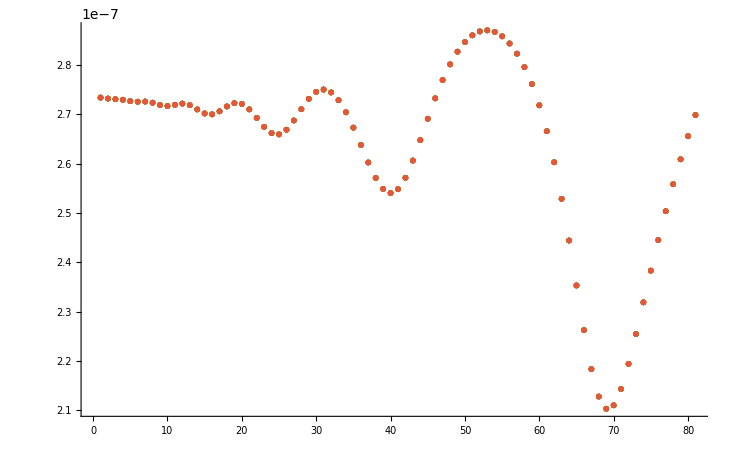

```mathematica
MatrixForm[M,
TableHeadings->{
{
Column[Table[StringJoin["n-th period n=",ToString[k]],{k,numperiodsinit,numperiodsfin}]]

(*StringJoin["n-th number of period of ext driv force n=",ToString[m1]],
StringJoin["n-th number of period of ext driv force n=",ToString[m1+1]]*)
},
{

StringJoin["Ext freq[kHz]=",ToString[freq1*fconf*10^-3]],
StringJoin["Ext freq[kHz]=",ToString[(freq1+stepfreq)*fconf*10^-3]]
}
}
]
```

( | Ext freq[kHz]=2000 | Ext freq[kHz]=4000 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
n-th number of period of ext driv force n=5
n-th number of period of ext driv force n=6
n-th number of period of ext driv force n=7
n-th number of period of ext driv force n=8
n-th number of period of ext driv force n=9
n-th number of period of ext driv force n=10
n-th number of period of ext driv force n=11
n-th number of period of ext driv force n=12
n-th number of period of ext driv force n=13
n-th number of period of ext driv force n=14
n-th number of period of ext driv force n=15 | 2.73412×10^-7 | 2.73217×10^-7 | 2.73096×10^-7 | 2.72972×10^-7 | 2.72697×10^-7 | 2.72573×10^-7 | 2.72606×10^-7 | 2.72372×10^-7 | 2.71896×10^-7 | 2.71698×10^-7 | 2.71954×10^-7 | 2.72192×10^-7 | 2.71872×10^-7 | 2.71015×10^-7 | 2.70194×10^-7 | 2.70015×10^-7 | 2.70628×10^-7 | 2.71615×10^-7 | 2.72288×10^-7 | 2.72128×10^-7 | 2.7103×10^-7 | 2.69295×10^-7 | 2.67481×10^-7 | 2.66209×10^-7 | 2.65958×10^-7 | 2.66891×10^-7 | 2.6877×10^-7 | 2.71063×10^-7 | 2.7316×10^-7 | 2.74579×10^-7 | 2.75042×10^-7 | 2.74462×10^-7 | 2.72882×10^-7 | 2.70433×10^-7 | 2.67317×10^-7 | 2.63804×10^-7 | 2.60252×10^-7 | 2.57113×10^-7 | 2.54893×10^-7 | 2.54049×10^-7 | 2.54826×10^-7 | 2.57145×10^-7 | 2.60635×10^-7 | 2.64787×10^-7 | 2.69117×10^-7 | 2.73259×10^-7 | 2.76978×10^-7 | 2.8015×10^-7 | 2.82723×10^-7 | 2.84685×10^-7 | 2.8605×10^-7 | 2.86834×10^-7 | 2.87056×10^-7 | 2.86725×10^-7 | 2.8584×10^-7 | 2.84383×10^-7 | 2.82321×10^-7 | 2.796×10^-7 | 2.76141×10^-7 | 2.71847×10^-7 | 2.66602×10^-7 | 2.60296×10^-7 | 2.52878×10^-7 | 2.44441×10^-7 | 2.35344×10^-7 | 2.26316×10^-7 | 2.18424×10^-7 | 2.12824×10^-7 | 2.10318×10^-7 | 2.11003×10^-7 | 2.14317×10^-7 | 2.19402×10^-7 | 2.25457×10^-7 | 2.31887×10^-7 | 2.38313×10^-7 | 2.44514×10^-7 | 2.50374×10^-7 | 2.55839×10^-7 | 2.60896×10^-7 | 2.65552×10^-7 | 2.69832×10^-7
 | 2.73412×10^-7 | 2.73217×10^-7 | 2.73096×10^-7 | 2.72972×10^-7 | 2.72697×10^-7 | 2.72573×10^-7 | 2.72606×10^-7 | 2.72372×10^-7 | 2.71896×10^-7 | 2.71698×10^-7 | 2.71954×10^-7 | 2.72192×10^-7 | 2.71872×10^-7 | 2.71015×10^-7 | 2.70194×10^-7 | 2.70015×10^-7 | 2.70628×10^-7 | 2.71615×10^-7 | 2.72288×10^-7 | 2.72128×10^-7 | 2.7103×10^-7 | 2.69295×10^-7 | 2.67481×10^-7 | 2.66209×10^-7 | 2.65958×10^-7 | 2.66891×10^-7 | 2.6877×10^-7 | 2.71063×10^-7 | 2.7316×10^-7 | 2.74579×10^-7 | 2.75042×10^-7 | 2.74462×10^-7 | 2.72882×10^-7 | 2.70433×10^-7 | 2.67317×10^-7 | 2.63804×10^-7 | 2.60252×10^-7 | 2.57113×10^-7 | 2.54893×10^-7 | 2.54049×10^-7 | 2.54826×10^-7 | 2.57145×10^-7 | 2.60635×10^-7 | 2.64787×10^-7 | 2.69117×10^-7 | 2.73259×10^-7 | 2.76978×10^-7 | 2.8015×10^-7 | 2.82723×10^-7 | 2.84685×10^-7 | 2.86049×10^-7 | 2.86834×10^-7 | 2.87056×10^-7 | 2.86725×10^-7 | 2.8584×10^-7 | 2.84383×10^-7 | 2.82321×10^-7 | 2.796×10^-7 | 2.76141×10^-7 | 2.71847×10^-7 | 2.66602×10^-7 | 2.60297×10^-7 | 2.52877×10^-7 | 2.44429×10^-7 | 2.35313×10^-7 | 2.26263×10^-7 | 2.18365×10^-7 | 2.12782×10^-7 | 2.10304×10^-7 | 2.11006×10^-7 | 2.14322×10^-7 | 2.19403×10^-7 | 2.25455×10^-7 | 2.31887×10^-7 | 2.38315×10^-7 | 2.44515×10^-7 | 2.50372×10^-7 | 2.55838×10^-7 | 2.60904×10^-7 | 2.65582×10^-7 | 2.69897×10^-7
 | 2.73412×10^-7 | 2.73217×10^-7 | 2.73096×10^-7 | 2.72972×10^-7 | 2.72697×10^-7 | 2.72573×10^-7 | 2.72606×10^-7 | 2.72372×10^-7 | 2.71896×10^-7 | 2.71698×10^-7 | 2.71954×10^-7 | 2.72192×10^-7 | 2.71872×10^-7 | 2.71015×10^-7 | 2.70194×10^-7 | 2.70015×10^-7 | 2.70628×10^-7 | 2.71615×10^-7 | 2.72288×10^-7 | 2.72128×10^-7 | 2.7103×10^-7 | 2.69295×10^-7 | 2.67481×10^-7 | 2.66209×10^-7 | 2.65958×10^-7 | 2.66891×10^-7 | 2.6877×10^-7 | 2.71063×10^-7 | 2.7316×10^-7 | 2.74579×10^-7 | 2.75042×10^-7 | 2.74462×10^-7 | 2.72882×10^-7 | 2.70433×10^-7 | 2.67317×10^-7 | 2.63804×10^-7 | 2.60252×10^-7 | 2.57113×10^-7 | 2.54893×10^-7 | 2.54049×10^-7 | 2.54826×10^-7 | 2.57145×10^-7 | 2.60635×10^-7 | 2.64787×10^-7 | 2.69117×10^-7 | 2.73259×10^-7 | 2.76978×10^-7 | 2.8015×10^-7 | 2.82723×10^-7 | 2.84685×10^-7 | 2.86049×10^-7 | 2.86834×10^-7 | 2.87056×10^-7 | 2.86725×10^-7 | 2.8584×10^-7 | 2.84383×10^-7 | 2.82321×10^-7 | 2.796×10^-7 | 2.76141×10^-7 | 2.71847×10^-7 | 2.66602×10^-7 | 2.60297×10^-7 | 2.52876×10^-7 | 2.44426×10^-7 | 2.35304×10^-7 | 2.26247×10^-7 | 2.18348×10^-7 | 2.12771×10^-7 | 2.103×10^-7 | 2.11006×10^-7 | 2.14322×10^-7 | 2.19403×10^-7 | 2.25455×10^-7 | 2.31887×10^-7 | 2.38315×10^-7 | 2.44515×10^-7 | 2.50372×10^-7 | 2.55838×10^-7 | 2.60903×10^-7 | 2.65577×10^-7 | 2.69882×10^-7
 | 2.73412×10^-7 | 2.73217×10^-7 | 2.73096×10^-7 | 2.72972×10^-7 | 2.72697×10^-7 | 2.72573×10^-7 | 2.72606×10^-7 | 2.72372×10^-7 | 2.71896×10^-7 | 2.71698×10^-7 | 2.71954×10^-7 | 2.72192×10^-7 | 2.71872×10^-7 | 2.71015×10^-7 | 2.70194×10^-7 | 2.70015×10^-7 | 2.70628×10^-7 | 2.71615×10^-7 | 2.72288×10^-7 | 2.72128×10^-7 | 2.7103×10^-7 | 2.69295×10^-7 | 2.67481×10^-7 | 2.66209×10^-7 | 2.65958×10^-7 | 2.66891×10^-7 | 2.6877×10^-7 | 2.71063×10^-7 | 2.7316×10^-7 | 2.74579×10^-7 | 2.75042×10^-7 | 2.74462×10^-7 | 2.72882×10^-7 | 2.70433×10^-7 | 2.67317×10^-7 | 2.63804×10^-7 | 2.60252×10^-7 | 2.57113×10^-7 | 2.54893×10^-7 | 2.54049×10^-7 | 2.54826×10^-7 | 2.57145×10^-7 | 2.60635×10^-7 | 2.64787×10^-7 | 2.69117×10^-7 | 2.73259×10^-7 | 2.76978×10^-7 | 2.8015×10^-7 | 2.82723×10^-7 | 2.84685×10^-7 | 2.86049×10^-7 | 2.86834×10^-7 | 2.87056×10^-7 | 2.86725×10^-7 | 2.8584×10^-7 | 2.84383×10^-7 | 2.82321×10^-7 | 2.796×10^-7 | 2.76141×10^-7 | 2.71847×10^-7 | 2.66602×10^-7 | 2.60297×10^-7 | 2.52876×10^-7 | 2.44426×10^-7 | 2.35302×10^-7 | 2.26243×10^-7 | 2.18343×10^-7 | 2.12768×10^-7 | 2.103×10^-7 | 2.11006×10^-7 | 2.14322×10^-7 | 2.19402×10^-7 | 2.25455×10^-7 | 2.31887×10^-7 | 2.38315×10^-7 | 2.44515×10^-7 | 2.50372×10^-7 | 2.55838×10^-7 | 2.60903×10^-7 | 2.65578×10^-7 | 2.69886×10^-7
 | 2.73412×10^-7 | 2.73217×10^-7 | 2.73096×10^-7 | 2.72972×10^-7 | 2.72697×10^-7 | 2.72573×10^-7 | 2.72606×10^-7 | 2.72372×10^-7 | 2.71896×10^-7 | 2.71698×10^-7 | 2.71954×10^-7 | 2.72192×10^-7 | 2.71872×10^-7 | 2.71015×10^-7 | 2.70194×10^-7 | 2.70015×10^-7 | 2.70628×10^-7 | 2.71615×10^-7 | 2.72288×10^-7 | 2.72128×10^-7 | 2.7103×10^-7 | 2.69295×10^-7 | 2.67481×10^-7 | 2.66209×10^-7 | 2.65958×10^-7 | 2.66891×10^-7 | 2.6877×10^-7 | 2.71063×10^-7 | 2.7316×10^-7 | 2.74579×10^-7 | 2.75042×10^-7 | 2.74462×10^-7 | 2.72882×10^-7 | 2.70433×10^-7 | 2.67317×10^-7 | 2.63804×10^-7 | 2.60252×10^-7 | 2.57113×10^-7 | 2.54893×10^-7 | 2.54049×10^-7 | 2.54826×10^-7 | 2.57145×10^-7 | 2.60635×10^-7 | 2.64787×10^-7 | 2.69117×10^-7 | 2.73259×10^-7 | 2.76978×10^-7 | 2.8015×10^-7 | 2.82723×10^-7 | 2.84685×10^-7 | 2.86049×10^-7 | 2.86834×10^-7 | 2.87056×10^-7 | 2.86725×10^-7 | 2.8584×10^-7 | 2.84383×10^-7 | 2.82321×10^-7 | 2.796×10^-7 | 2.76141×10^-7 | 2.71847×10^-7 | 2.66602×10^-7 | 2.60297×10^-7 | 2.52876×10^-7 | 2.44425×10^-7 | 2.35301×10^-7 | 2.26242×10^-7 | 2.18342×10^-7 | 2.12768×10^-7 | 2.103×10^-7 | 2.11006×10^-7 | 2.14322×10^-7 | 2.19402×10^-7 | 2.25455×10^-7 | 2.31887×10^-7 | 2.38315×10^-7 | 2.44515×10^-7 | 2.50372×10^-7 | 2.55838×10^-7 | 2.60903×10^-7 | 2.65577×10^-7 | 2.69885×10^-7
 | 2.73412×10^-7 | 2.73217×10^-7 | 2.73096×10^-7 | 2.72972×10^-7 | 2.72697×10^-7 | 2.72573×10^-7 | 2.72606×10^-7 | 2.72372×10^-7 | 2.71896×10^-7 | 2.71698×10^-7 | 2.71954×10^-7 | 2.72192×10^-7 | 2.71872×10^-7 | 2.71015×10^-7 | 2.70194×10^-7 | 2.70015×10^-7 | 2.70628×10^-7 | 2.71615×10^-7 | 2.72288×10^-7 | 2.72128×10^-7 | 2.7103×10^-7 | 2.69295×10^-7 | 2.67481×10^-7 | 2.66209×10^-7 | 2.65958×10^-7 | 2.66891×10^-7 | 2.6877×10^-7 | 2.71063×10^-7 | 2.7316×10^-7 | 2.74579×10^-7 | 2.75042×10^-7 | 2.74462×10^-7 | 2.72882×10^-7 | 2.70433×10^-7 | 2.67317×10^-7 | 2.63804×10^-7 | 2.60252×10^-7 | 2.57113×10^-7 | 2.54893×10^-7 | 2.54049×10^-7 | 2.54826×10^-7 | 2.57145×10^-7 | 2.60635×10^-7 | 2.64787×10^-7 | 2.69117×10^-7 | 2.73259×10^-7 | 2.76978×10^-7 | 2.8015×10^-7 | 2.82723×10^-7 | 2.84685×10^-7 | 2.86049×10^-7 | 2.86834×10^-7 | 2.87056×10^-7 | 2.86725×10^-7 | 2.8584×10^-7 | 2.84383×10^-7 | 2.82321×10^-7 | 2.796×10^-7 | 2.76141×10^-7 | 2.71847×10^-7 | 2.66602×10^-7 | 2.60297×10^-7 | 2.52876×10^-7 | 2.44425×10^-7 | 2.35301×10^-7 | 2.26241×10^-7 | 2.18341×10^-7 | 2.12767×10^-7 | 2.10299×10^-7 | 2.11006×10^-7 | 2.14322×10^-7 | 2.19402×10^-7 | 2.25455×10^-7 | 2.31887×10^-7 | 2.38315×10^-7 | 2.44515×10^-7 | 2.50372×10^-7 | 2.55838×10^-7 | 2.60903×10^-7 | 2.65577×10^-7 | 2.69885×10^-7
 | 2.73412×10^-7 | 2.73217×10^-7 | 2.73096×10^-7 | 2.72972×10^-7 | 2.72697×10^-7 | 2.72573×10^-7 | 2.72606×10^-7 | 2.72372×10^-7 | 2.71896×10^-7 | 2.71698×10^-7 | 2.71954×10^-7 | 2.72192×10^-7 | 2.71872×10^-7 | 2.71015×10^-7 | 2.70194×10^-7 | 2.70015×10^-7 | 2.70628×10^-7 | 2.71615×10^-7 | 2.72288×10^-7 | 2.72128×10^-7 | 2.7103×10^-7 | 2.69295×10^-7 | 2.67481×10^-7 | 2.66209×10^-7 | 2.65958×10^-7 | 2.66891×10^-7 | 2.6877×10^-7 | 2.71063×10^-7 | 2.7316×10^-7 | 2.74579×10^-7 | 2.75042×10^-7 | 2.74462×10^-7 | 2.72882×10^-7 | 2.70433×10^-7 | 2.67317×10^-7 | 2.63804×10^-7 | 2.60252×10^-7 | 2.57113×10^-7 | 2.54893×10^-7 | 2.54049×10^-7 | 2.54826×10^-7 | 2.57145×10^-7 | 2.60635×10^-7 | 2.64787×10^-7 | 2.69117×10^-7 | 2.73259×10^-7 | 2.76978×10^-7 | 2.8015×10^-7 | 2.82723×10^-7 | 2.84685×10^-7 | 2.86049×10^-7 | 2.86834×10^-7 | 2.87056×10^-7 | 2.86725×10^-7 | 2.8584×10^-7 | 2.84383×10^-7 | 2.82321×10^-7 | 2.796×10^-7 | 2.76141×10^-7 | 2.71847×10^-7 | 2.66602×10^-7 | 2.60297×10^-7 | 2.52876×10^-7 | 2.44425×10^-7 | 2.35301×10^-7 | 2.26241×10^-7 | 2.18341×10^-7 | 2.12767×10^-7 | 2.10299×10^-7 | 2.11006×10^-7 | 2.14322×10^-7 | 2.19402×10^-7 | 2.25455×10^-7 | 2.31887×10^-7 | 2.38315×10^-7 | 2.44515×10^-7 | 2.50372×10^-7 | 2.55838×10^-7 | 2.60903×10^-7 | 2.65577×10^-7 | 2.69885×10^-7
 | 2.73412×10^-7 | 2.73217×10^-7 | 2.73096×10^-7 | 2.72972×10^-7 | 2.72697×10^-7 | 2.72573×10^-7 | 2.72606×10^-7 | 2.72372×10^-7 | 2.71896×10^-7 | 2.71698×10^-7 | 2.71954×10^-7 | 2.72192×10^-7 | 2.71872×10^-7 | 2.71015×10^-7 | 2.70194×10^-7 | 2.70015×10^-7 | 2.70628×10^-7 | 2.71615×10^-7 | 2.72288×10^-7 | 2.72128×10^-7 | 2.7103×10^-7 | 2.69295×10^-7 | 2.67481×10^-7 | 2.66209×10^-7 | 2.65958×10^-7 | 2.66891×10^-7 | 2.6877×10^-7 | 2.71063×10^-7 | 2.7316×10^-7 | 2.74579×10^-7 | 2.75042×10^-7 | 2.74462×10^-7 | 2.72882×10^-7 | 2.70433×10^-7 | 2.67317×10^-7 | 2.63804×10^-7 | 2.60252×10^-7 | 2.57113×10^-7 | 2.54893×10^-7 | 2.54049×10^-7 | 2.54826×10^-7 | 2.57145×10^-7 | 2.60635×10^-7 | 2.64787×10^-7 | 2.69117×10^-7 | 2.73259×10^-7 | 2.76978×10^-7 | 2.8015×10^-7 | 2.82723×10^-7 | 2.84685×10^-7 | 2.86049×10^-7 | 2.86834×10^-7 | 2.87056×10^-7 | 2.86725×10^-7 | 2.8584×10^-7 | 2.84383×10^-7 | 2.82321×10^-7 | 2.796×10^-7 | 2.76141×10^-7 | 2.71847×10^-7 | 2.66602×10^-7 | 2.60297×10^-7 | 2.52876×10^-7 | 2.44425×10^-7 | 2.35301×10^-7 | 2.26241×10^-7 | 2.18341×10^-7 | 2.12767×10^-7 | 2.10299×10^-7 | 2.11006×10^-7 | 2.14322×10^-7 | 2.19402×10^-7 | 2.25455×10^-7 | 2.31887×10^-7 | 2.38315×10^-7 | 2.44515×10^-7 | 2.50372×10^-7 | 2.55838×10^-7 | 2.60903×10^-7 | 2.65577×10^-7 | 2.69885×10^-7
 | 2.73412×10^-7 | 2.73217×10^-7 | 2.73096×10^-7 | 2.72972×10^-7 | 2.72697×10^-7 | 2.72573×10^-7 | 2.72606×10^-7 | 2.72372×10^-7 | 2.71896×10^-7 | 2.71698×10^-7 | 2.71954×10^-7 | 2.72192×10^-7 | 2.71872×10^-7 | 2.71015×10^-7 | 2.70194×10^-7 | 2.70015×10^-7 | 2.70628×10^-7 | 2.71615×10^-7 | 2.72288×10^-7 | 2.72128×10^-7 | 2.7103×10^-7 | 2.69295×10^-7 | 2.67481×10^-7 | 2.66209×10^-7 | 2.65958×10^-7 | 2.66891×10^-7 | 2.6877×10^-7 | 2.71063×10^-7 | 2.7316×10^-7 | 2.74579×10^-7 | 2.75042×10^-7 | 2.74462×10^-7 | 2.72882×10^-7 | 2.70433×10^-7 | 2.67317×10^-7 | 2.63804×10^-7 | 2.60252×10^-7 | 2.57113×10^-7 | 2.54893×10^-7 | 2.54049×10^-7 | 2.54826×10^-7 | 2.57145×10^-7 | 2.60635×10^-7 | 2.64787×10^-7 | 2.69117×10^-7 | 2.73259×10^-7 | 2.76978×10^-7 | 2.8015×10^-7 | 2.82723×10^-7 | 2.84685×10^-7 | 2.86049×10^-7 | 2.86834×10^-7 | 2.87056×10^-7 | 2.86725×10^-7 | 2.8584×10^-7 | 2.84383×10^-7 | 2.82321×10^-7 | 2.796×10^-7 | 2.76141×10^-7 | 2.71847×10^-7 | 2.66602×10^-7 | 2.60297×10^-7 | 2.52876×10^-7 | 2.44425×10^-7 | 2.35301×10^-7 | 2.26241×10^-7 | 2.18341×10^-7 | 2.12767×10^-7 | 2.10299×10^-7 | 2.11006×10^-7 | 2.14322×10^-7 | 2.19402×10^-7 | 2.25455×10^-7 | 2.31887×10^-7 | 2.38315×10^-7 | 2.44515×10^-7 | 2.50372×10^-7 | 2.55838×10^-7 | 2.60903×10^-7 | 2.65577×10^-7 | 2.69885×10^-7
 | 2.73412×10^-7 | 2.73217×10^-7 | 2.73096×10^-7 | 2.72972×10^-7 | 2.72697×10^-7 | 2.72573×10^-7 | 2.72606×10^-7 | 2.72372×10^-7 | 2.71896×10^-7 | 2.71698×10^-7 | 2.71954×10^-7 | 2.72192×10^-7 | 2.71872×10^-7 | 2.71015×10^-7 | 2.70194×10^-7 | 2.70015×10^-7 | 2.70628×10^-7 | 2.71615×10^-7 | 2.72288×10^-7 | 2.72128×10^-7 | 2.7103×10^-7 | 2.69295×10^-7 | 2.67481×10^-7 | 2.66209×10^-7 | 2.65958×10^-7 | 2.66891×10^-7 | 2.6877×10^-7 | 2.71063×10^-7 | 2.7316×10^-7 | 2.74579×10^-7 | 2.75042×10^-7 | 2.74462×10^-7 | 2.72882×10^-7 | 2.70433×10^-7 | 2.67317×10^-7 | 2.63804×10^-7 | 2.60252×10^-7 | 2.57113×10^-7 | 2.54893×10^-7 | 2.54049×10^-7 | 2.54826×10^-7 | 2.57145×10^-7 | 2.60635×10^-7 | 2.64787×10^-7 | 2.69117×10^-7 | 2.73259×10^-7 | 2.76978×10^-7 | 2.8015×10^-7 | 2.82723×10^-7 | 2.84685×10^-7 | 2.86049×10^-7 | 2.86834×10^-7 | 2.87056×10^-7 | 2.86725×10^-7 | 2.8584×10^-7 | 2.84383×10^-7 | 2.82321×10^-7 | 2.796×10^-7 | 2.76141×10^-7 | 2.71847×10^-7 | 2.66602×10^-7 | 2.60297×10^-7 | 2.52876×10^-7 | 2.44425×10^-7 | 2.35301×10^-7 | 2.26241×10^-7 | 2.18341×10^-7 | 2.12767×10^-7 | 2.10299×10^-7 | 2.11006×10^-7 | 2.14322×10^-7 | 2.19402×10^-7 | 2.25455×10^-7 | 2.31887×10^-7 | 2.38315×10^-7 | 2.44515×10^-7 | 2.50372×10^-7 | 2.55838×10^-7 | 2.60903×10^-7 | 2.65577×10^-7 | 2.69885×10^-7
 | 2.73412×10^-7 | 2.73217×10^-7 | 2.73096×10^-7 | 2.72972×10^-7 | 2.72697×10^-7 | 2.72573×10^-7 | 2.72606×10^-7 | 2.72372×10^-7 | 2.71896×10^-7 | 2.71698×10^-7 | 2.71954×10^-7 | 2.72192×10^-7 | 2.71872×10^-7 | 2.71015×10^-7 | 2.70194×10^-7 | 2.70015×10^-7 | 2.70628×10^-7 | 2.71615×10^-7 | 2.72288×10^-7 | 2.72128×10^-7 | 2.7103×10^-7 | 2.69295×10^-7 | 2.67481×10^-7 | 2.66209×10^-7 | 2.65958×10^-7 | 2.66891×10^-7 | 2.6877×10^-7 | 2.71063×10^-7 | 2.7316×10^-7 | 2.74579×10^-7 | 2.75042×10^-7 | 2.74462×10^-7 | 2.72882×10^-7 | 2.70433×10^-7 | 2.67317×10^-7 | 2.63804×10^-7 | 2.60252×10^-7 | 2.57113×10^-7 | 2.54893×10^-7 | 2.54049×10^-7 | 2.54826×10^-7 | 2.57145×10^-7 | 2.60635×10^-7 | 2.64787×10^-7 | 2.69117×10^-7 | 2.73259×10^-7 | 2.76978×10^-7 | 2.8015×10^-7 | 2.82723×10^-7 | 2.84685×10^-7 | 2.86049×10^-7 | 2.86834×10^-7 | 2.87056×10^-7 | 2.86725×10^-7 | 2.8584×10^-7 | 2.84383×10^-7 | 2.82321×10^-7 | 2.796×10^-7 | 2.76141×10^-7 | 2.71847×10^-7 | 2.66602×10^-7 | 2.60297×10^-7 | 2.52876×10^-7 | 2.44425×10^-7 | 2.35301×10^-7 | 2.26241×10^-7 | 2.18341×10^-7 | 2.12767×10^-7 | 2.10299×10^-7 | 2.11006×10^-7 | 2.14322×10^-7 | 2.19402×10^-7 | 2.25455×10^-7 | 2.31887×10^-7 | 2.38315×10^-7 | 2.44515×10^-7 | 2.50372×10^-7 | 2.55838×10^-7 | 2.60903×10^-7 | 2.65577×10^-7 | 2.69885×10^-7)

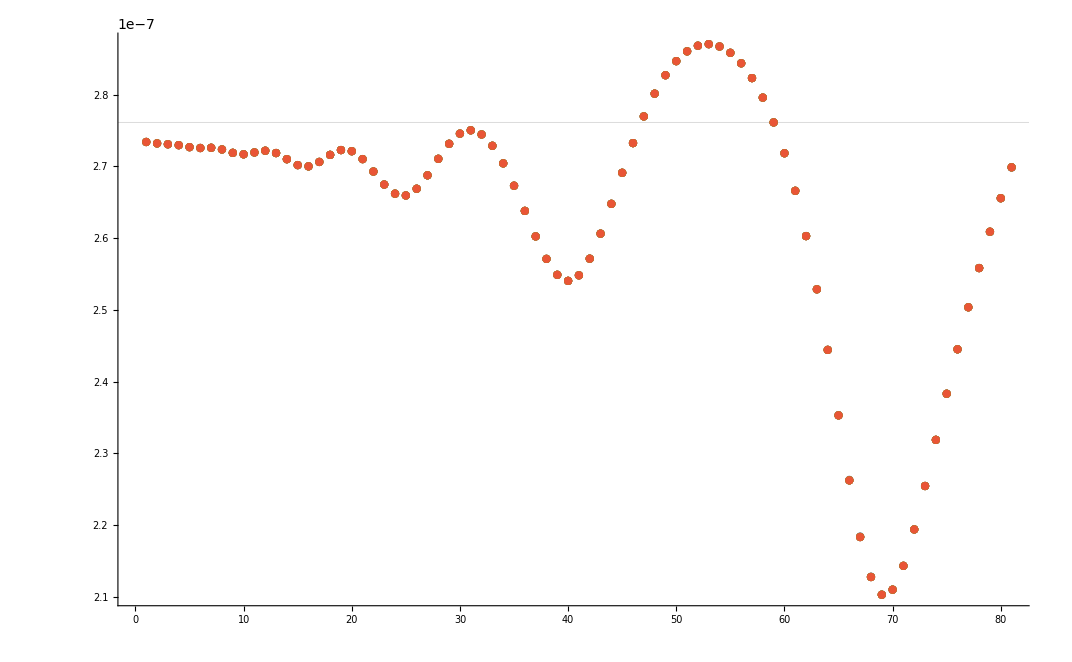

```mathematica
MatrixForm[M,
TableHeadings->{
{
Column[Table[StringJoin["n-th number of period of ext driv force n=",ToString[k]],{k,m1,m2}]]

(*StringJoin["n-th number of period of ext driv force n=",ToString[m1]],
StringJoin["n-th number of period of ext driv force n=",ToString[m1+1]]*)
},
{
StringJoin["Ext freq[kHz]=",ToString[k1*fconf*10^-3]],
StringJoin["Ext freq[kHz]=",ToString[(k1+1)*fconf*10^-3]]
}
}
]
ListPlot[M,GridLines->{
{}
,{Rb0  }}]
```

```mathematica
1.timeintegr
1./1000*timeintegr
FindPeaks[Table[Rb[t]/.ndsmodconfdonw[[1]],{t,0,1.0timeintegr,1.0/1000*timeintegr}]]
```

0.0001

1.×10^-7

```mathematica
sol=ParametricNDSolve[{y'[t]==a y[t],y[0]==1},y,{t,0,10},{a}];
Manipulate[
Plot[
{y[i][t]/.sol(*,
y[2][t]/.sol,
Exp[2t]*)},{t,0,1},
PlotRange->{{0,1},{0,10}},
PlotLabels->Automatic
],
{i,1,4,1}
]
```

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
Manipulate[
Module[
{sol,iterate,pts,fsol},

sol[c_]:=NDSolve[{
x'[t]==-(y[t]+z[t]),
y'[t]== x[t]+a y[t],
z'[t]== b+x[t] z[t]-c z[t],

x[0]== -1,
y[0]== 0,
z[0]== 0},
{x[t],y[t],z[t]},
{t,0,310}];

iterate=Compile[{c},{fsol=sol[c];
Map[{c,#}&,FindMaxValue[z[t]/.fsol,{t,#,#+10}]&/@Table[i,{i,200,300.0,10}]]}
               ];

pts=Quiet[Flatten[Table[iterate[c],{c,1,5.8,0.05}],1]];

ListPlot[pts,
(*PlotStyle->Table[{PointSize[0.01],RGBColor[.49,0,0]},{i,1,Length[pts]}],*)
Frame-> True,ImageSize-> {400,350},
FrameLabel->{Style["c",Italic],Style["z",Italic]},
ImageSize-> {500,500},
AspectRatio-> 1,
ImagePadding->{{35,10},{35,10}}]
],

{{a,0.25,"a"},0.1,0.4,0.05,Appearance-> "Labeled"},
{{b,0.3,"b"},0.1,0.3,0.05,Appearance-> "Labeled"},
ControlPlacement-> Top,SynchronousUpdating -> False]
```

```mathematica
(*Phase diagram*)
(*Text[" =Number of periods"(0.2*0.0025timeintegr)/(1/fconf)]

s2=Rb/.First@ndsmodconfdonw;
Text["minimum radius "]  Min[s2["ValuesOnGrid"]]
Text["maximum radius"]  Max[s2["ValuesOnGrid"]]
s3=Rb'/.First@ndsmodconfdonw;
Text["minimum velocity "]  Min[s3["ValuesOnGrid"]]
Text["maximum velocity"]  Max[s3["ValuesOnGrid"]]

Show[
ParametricPlot[Evaluate[
{
10^7 Rb[t]/.ndsmodconfdonw[[1]],
Rb'[t]/.ndsmodconfdonw[[1]]
}
],{t,0,timeintegr},
(*Frame ->  True,*)
PlotStyle->Directive[Blue,Medium],
(*PlotStyle->{
Thickness[Large]
},*)
PlotPoints->30*Npoints,

AxesLabel->{"R_b[m]*10^-7","V_b[m/s]"},
LabelStyle->Directive[Black,Bold,16],
GridLinesStyle->Directive[Dashed],
PlotLegends->{
StringJoin["Confined liquid, driving freq [kHz] f=",ToString[fconf*10^-3]]
},
(*ColorFunction->"Rainbow",*)

(*PlotRange->{{0,1.04*10^7 Max[s2["ValuesOnGrid"]]},{-1/100*180,1/100*160}},*)
(*PlotRange->{{0,10^7*1.3RadiusC},{-9,5.5}},*)
(*PlotRange->{{10^7*0.95Rb0,10^7*1.05Rb0},{-0.1,0.1}},*)


PlotRange->{{0*10^7 Max[s2["ValuesOnGrid"]],1.2*10^7 Max[s2["ValuesOnGrid"]]},{1.1Min[s3["ValuesOnGrid"]],1.1Max[s3["ValuesOnGrid"]]}},
GridLines->{{10^7 Rb0,
10^7 RadiusA,
10^7 RadiusB,
10^7 RadiusD,
10^7 RadiusC
},
{
Min[s3["ValuesOnGrid"]],
Max[s3["ValuesOnGrid"]]
}
}
],
Graphics[{Red,Thickness[Large],Line[{{10^7 Rb0,-50},{10^7 Rb0,50}}]}],
Graphics[{Green,Thickness[Large],Line[{{10^7 Reqright4[Rl0,Rb0,pl11],-50},{10^7 Reqright4[Rl0,Rb0,pl11],50}}]}],
Graphics[{Green,Thickness[Large],Line[{{10^7 Reqright6[Rl0,Rb0,(1+Ampl)*pl1],-50},{10^7 Reqright6[Rl0,Rb0,(1+Ampl)*pl1],50}}]}],
Graphics[{Yellow,Thickness[Large],Line[{{10^7 Max[s2["ValuesOnGrid"]],-50},{10^7 Max[s2["ValuesOnGrid"]],50}}]}]
]*)
(*\Phase diagram*)
```

```mathematica
Text["First, having a dataset of length N sampled with a time step Δt, the Fourier (FFT) can resolve frequencies ωk from the interval (−ω_Nyq,ω_Nyq), where ω_Nyq=1/(2  Δt) is the Nyquist frequency, and the frequencies are ω_k=k/T, where T is the length of the time series and k is an integer from the range (−N/2,N/2)."]
```

First, having a dataset of length N sampled with a time step Δt, the Fourier (FFT) can resolve frequencies ωk from the interval (−ω_Nyq,ω_Nyq), where ω_Nyq=1/(2  Δt) is the Nyquist frequency, and the frequencies are ω_k=k/T, where T is the length of the time series and k is an integer from the range (−N/2,N/2).

200. =Number of periods and frequency of the external driving force

109890. =Number of points

549.451 =Number of points for a period

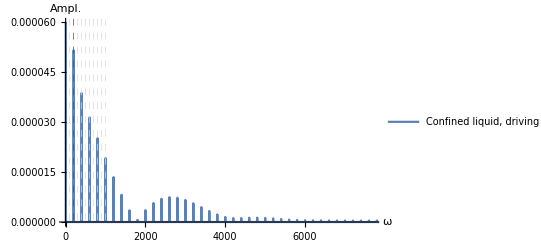

0.000138139  =Max value of Ampl. at zero frequency term

```mathematica
Numberpoints=2*10^-8;
Text["=Number of periods and frequency of the external driving force"(1.0*timeintegr)/(1/fconf)]
Text["=Number of points"(1.0*timeintegr)/Numberpoints]
Text["=Number of points for a period"(timeintegr/Numberpoints)/((1.0*timeintegr)/(1/fconf))]

testData=Table[Rb[t]/.ndsmodconfdonw[[1]],{t,0,timeintegr,Numberpoints}];

ListLinePlot[
Abs[Fourier[testData(*,FourierParameters->{1,1}*)]],

LabelStyle->Directive[Black,Bold,16],
GridLinesStyle->Directive[Dashed],
PlotStyle->{
Thickness[Large]
},
(*MaxPlotPoints->10^12(*3Npoints*),*)
PlotLegends->{
(*StringJoin["Bulk liquid, driving freq [kHz] f=",ToString[fbulk*10^-3]],*)
StringJoin["Confined liquid, driving freq [kHz] f=",ToString[fconf*10^-3],
", Time of integration [ms] t_INTEGR=",ToString[timeintegr*1.0*10^3]]
},
(*InterpolationOrder->15,*)
(*PlotRange->{{0,100},{-22,-5}},*)
(*PlotRange->{{0,
3000},Full},*)
PlotRange->{{0,(0.07timeintegr)/Numberpoints},{0,6*10^-5}},
(*PlotRange->Full,*)
AxesLabel->{"ω","Ampl."},
GridLines->{{
{timeintegr*fconf,Red},
0.5timeintegr*fconf,
1.5timeintegr*fconf,
2timeintegr*fconf,
2.5timeintegr*fconf,
3timeintegr*fconf,
3.5timeintegr*fconf,
4timeintegr*fconf,
4.5timeintegr*fconf,
5timeintegr*fconf
},
{}
}
]
Text[" =Max value of Ampl. at zero frequency term"Max[Abs[Fourier[testData]]]]
```

```mathematica
timeintegr*fconf
```

10000

```mathematica
60(1.0*timeintegr)/(1/fconf)
```

600000.

```mathematica
550000./9000
```

61.1111

```mathematica
f[a_][x_]:=a*x-1.19 x^3;
cps[a_]=x/.Quiet[Solve[D[f[a][x],x]==0,x],Solve::ratnz]

criticalOrbits[a_,cp_]:=Module[{try},If[Head[cp]===Real,try=NestWhileList[f[a],cp,Abs[#]<100&,1,500];
If[Abs[Last[try]]≥100,try={},try=Drop[{a,#}&/@try,100]],{}]];
points[k_]:=Partition[Flatten[Table[criticalOrbits[a,cps[a][[k]]],{a,-2,4,0.002}]],2]

Graphics[{Opacity[0.02],PointSize[0.002],Table[{ColorData[1,k],Point[points[k]]},{k,1,Length[cps[a]]}]},Frame->True]
```

{-0.529256 √a,0.529256 √a}

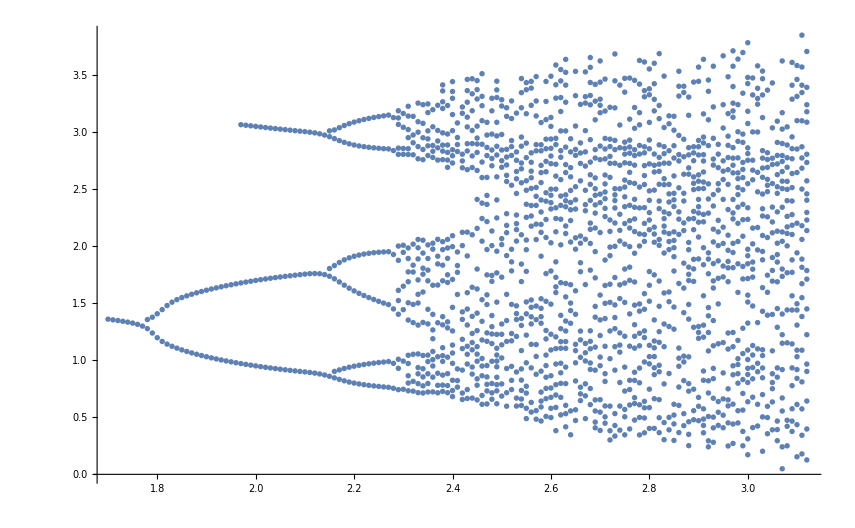

```mathematica
G=3.55;ω=2*Pi*12*10^6;
tab=Table[
{sol,points}=Reap@NDSolveValue[
{
v'[t]==2*G*BesselJ[1,v[t-τ]] Cos[ω*τ]-v[t],v[t/;t≤0]==0.001,
WhenEvent[v'[t]>0,If[t>150,Sow[v[t]]]]
},{v,v'},{t,0,250}
];

{τ,#}&/@Union[Flatten[points],SameTest->(Abs[#1-#2]<.05&)],{τ,1.7,2.4,.01}
];
ListPlot[Flatten[tab,1]]
```

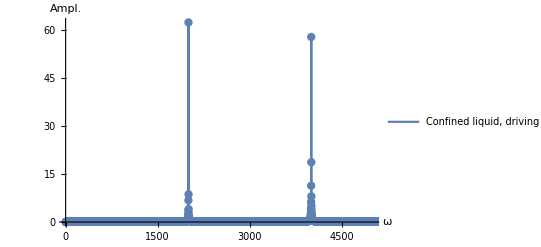

```mathematica
NN=2^14;
T=2000;

testData=Table[Cos[2Pi*t]+Cos[4Pi*t],{t,0,T,T/NN}];
ListLinePlot[
Abs[Fourier[testData(*,FourierParameters->{1,1}*)]],

LabelStyle->Directive[Black,Bold,16],
GridLinesStyle->Directive[Dashed],
(*MaxPlotPoints->10^12(*3Npoints*),*)
PlotLegends->{
(*StringJoin["Bulk liquid, driving freq [kHz] f=",ToString[fbulk*10^-3]],*)
StringJoin["Confined liquid, driving freq [kHz] f=",ToString[fconf*10^-3]]
},
(*InterpolationOrder->15,*)
(*PlotRange->{{0,100},{-22,-5}},*)
PlotRange->{{0000,5000},Full},
(*DataRange->{0,NN/T},*)
(*ScalingFunctions->{None,"Log"},*)
Mesh->Full,
MeshStyle->PointSize[Medium],
(*PlotRange->Full,*)
AxesLabel->{"ω","Ampl."}
]
```

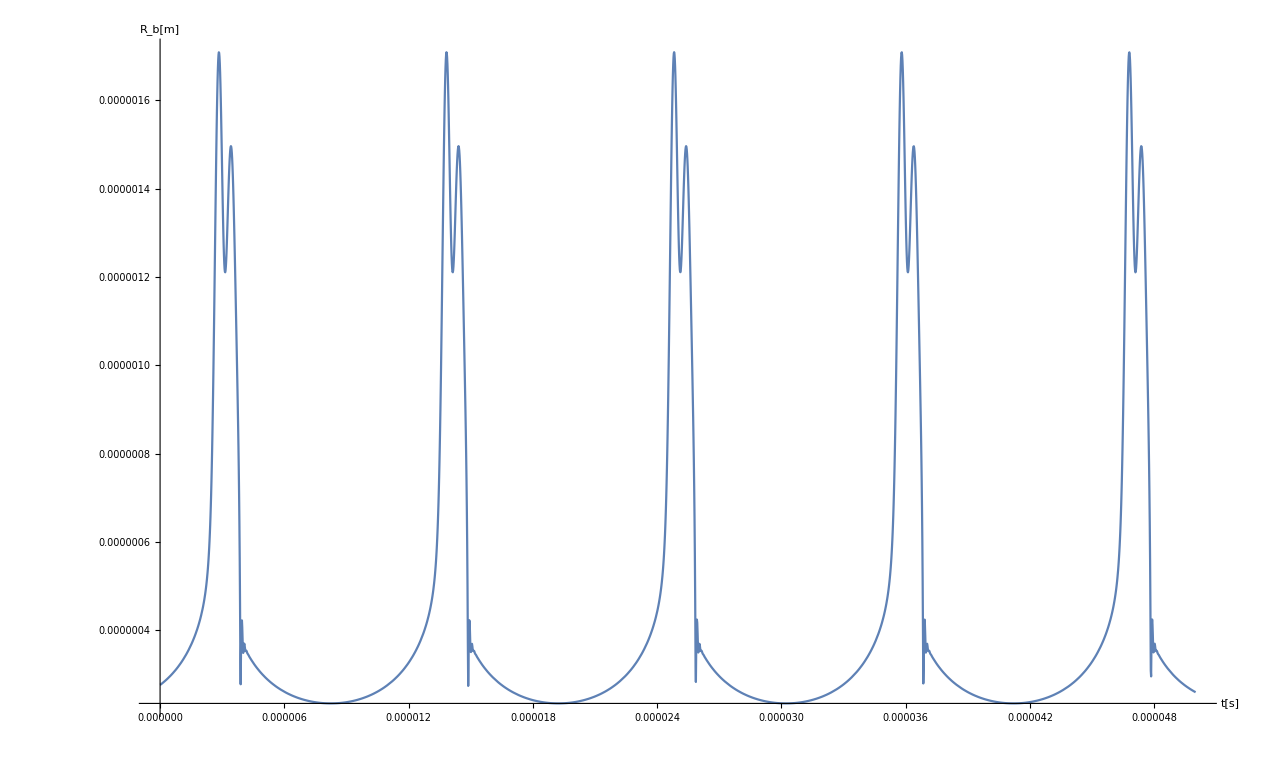

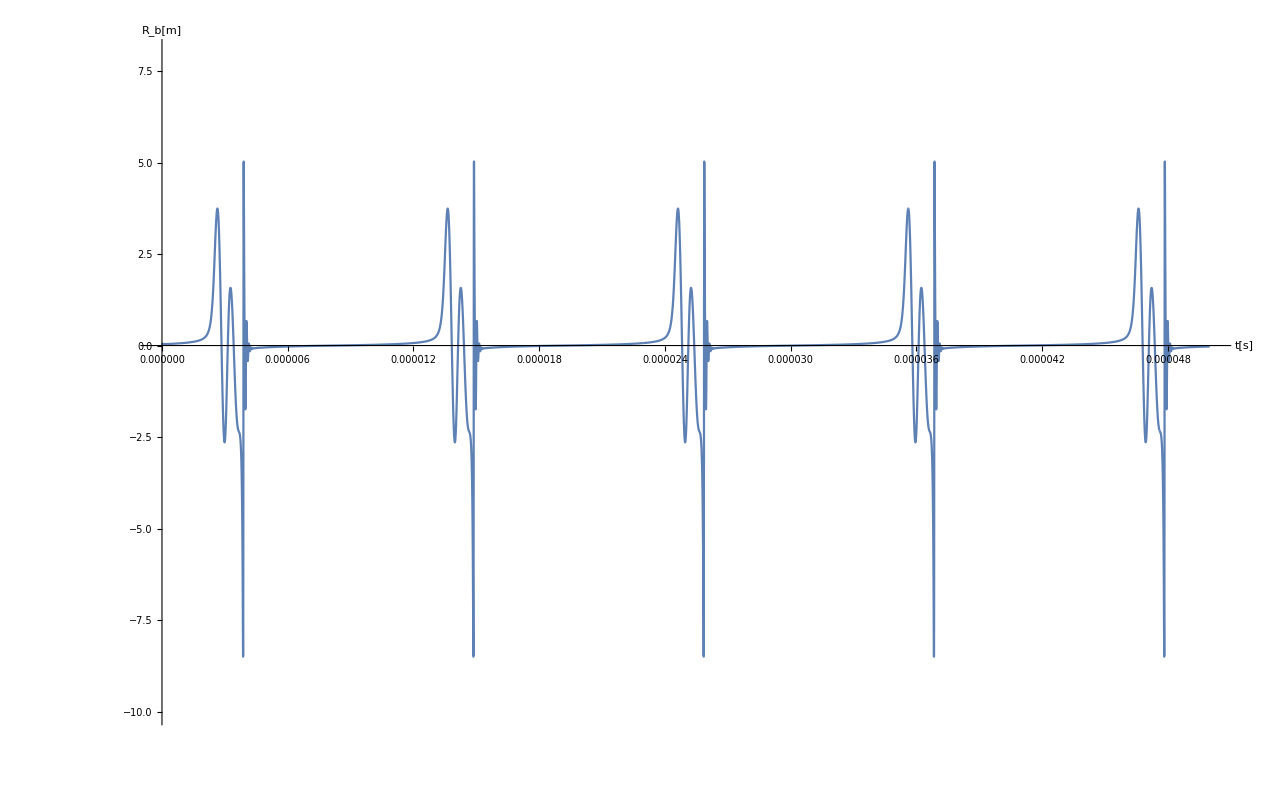

```mathematica
Plot[{
Rb[t]/.ndsmodconfdonw
},
{t,0,0.5timeintegr},
AxesLabel->{"t[s]","R_b[m]"},
LabelStyle->Directive[Black,Bold,16],
GridLinesStyle->Directive[Dashed],
PlotRange->Full
]
Plot[{
Rb'[t]/.ndsmodconfdonw
},
{t,0,0.5timeintegr},
AxesLabel->{"t[s]","R_b[m]"},
LabelStyle->Directive[Black,Bold,16],
GridLinesStyle->Directive[Dashed],
PlotPoints->5*Npoints,
PlotRange->{-10,8}
]
```

```mathematica
Clear[testData]
```

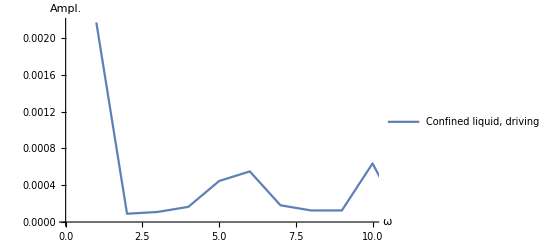

```mathematica
testData=Table[Rb[t]/.ndsmodconfdonw[[1]],{t,0,0.5timeintegr,1*10^-8}];
ListLinePlot[
Abs[Fourier[testData,FourierParameters->{1,1}]],

LabelStyle->Directive[Black,Bold,16],
GridLinesStyle->Directive[Dashed],
(*MaxPlotPoints->10^12(*3Npoints*),*)
PlotLegends->{
(*StringJoin["Bulk liquid, driving freq [kHz] f=",ToString[fbulk*10^-3]],*)
StringJoin["Confined liquid, driving freq [kHz] f=",ToString[fconf*10^-3]]
},
(*InterpolationOrder->15,*)
(*PlotRange->{{0,100},{-22,-5}},*)
PlotRange->{{0,10},Full},
AxesLabel->{"ω","Ampl."}
]
```

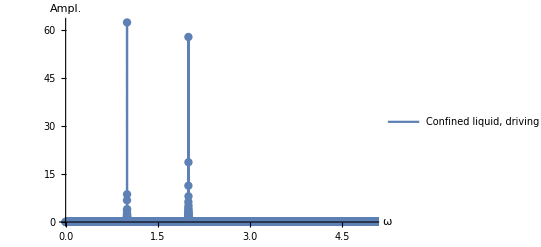

```mathematica
NN=2^14;
T=2000;

testData=Table[Cos[2Pi*t]+Cos[4Pi*t],{t,0,T,T/NN}];
ListLinePlot[
Abs[Fourier[testData(*,FourierParameters->{1,1}*)]],

LabelStyle->Directive[Black,Bold,16],
GridLinesStyle->Directive[Dashed],
(*MaxPlotPoints->10^12(*3Npoints*),*)
PlotLegends->{
(*StringJoin["Bulk liquid, driving freq [kHz] f=",ToString[fbulk*10^-3]],*)
StringJoin["Confined liquid, driving freq [kHz] f=",ToString[fconf*10^-3]]
},
(*InterpolationOrder->15,*)
(*PlotRange->{{0,100},{-22,-5}},*)
PlotRange->{{0,5},Full},
DataRange->{0,NN/T},
(*ScalingFunctions->{None,"Log"},*)
Mesh->Full,
MeshStyle->PointSize[Medium],
(*PlotRange->Full,*)
AxesLabel->{"ω","Ampl."}
]
```

```mathematica
fconf
1./fconf
```

54600000

1.8315×10^-8

```mathematica
.
```

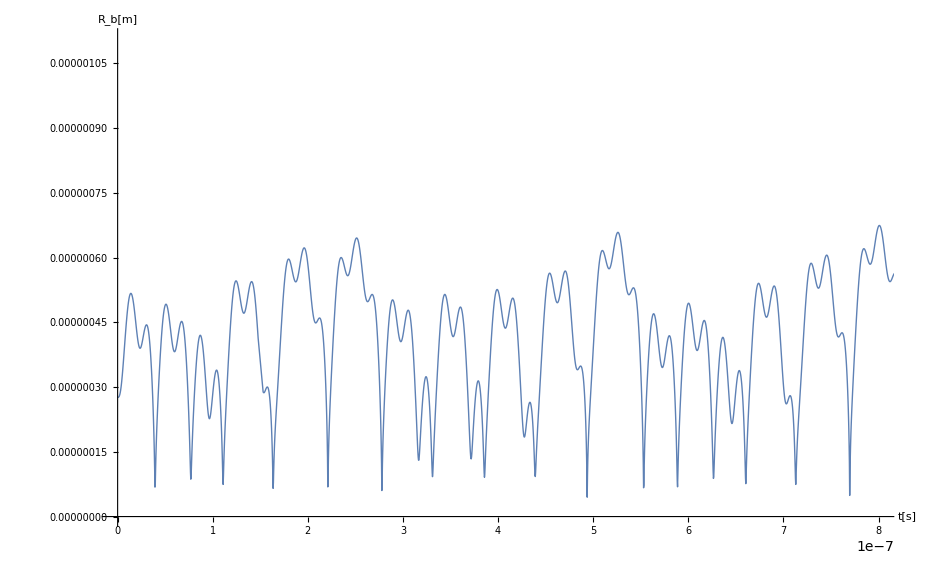

```mathematica
Plot[{

Rb[t]/.ndsmodconfdonw[[1]]
},
{t,0,1*10^-6},
AxesLabel->{"t[s]","R_b[m]"},
LabelStyle->Directive[Black,Bold,16],
GridLinesStyle->Directive[Dashed],

(*General view*)
PlotRange->{{0,0.8*10^-6},{0.95Rb0*0,0.8RadiusC}},

(*PlotRange->{{0,0.8*10^-6},{0.95Rb0*0,0.8RadiusC}},*)
(*PlotRange->{{0,5*10^-6},{0.95Rb0*0,1.2RadiusC}},*)
(*PlotRange->{{0*10^-6,1.5*10^-6},{0.95Rb0*0,1.15RadiusC}},*)
(*PlotRange->{{4.67*10^-6,4.78*10^-6(*0.2timeintegr*)},{0.95Rb0*0,2.09*10^-7(*29.5RadiusC*)}},*)
PlotStyle->{
Thickness[Large]
}
(*PlotPoints->2*Npoints*)

]
```

```mathematica
ListLinePlot[Abs[Fourier[testData]],PlotRange->Full]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

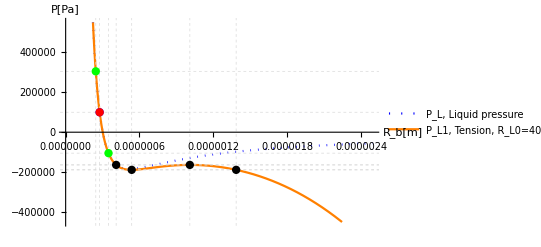

```mathematica
(**)
(*Data for an initial expansion*)
Text["The middle pressure, [Pa]:"];
pl1=P0 (*middle pressure*);
(*Data for final expansion*)
Text["The amplitude pressure above middle, [Pa]:"];
pl11=3.05P0;(*amplitude pressure above middle*);
Ampl=1.0*(pl1-pl11)/pl1;
(*Confined liquid sinus function for liquid element*)
Rl1[t_]:=(Rl0^3+(P0-pl1*(1+Ampl*Sin[2Pi*fconf*t]))*((Rl0^3-Rb0^3)/Ev))^(1/3)
dRl1[t_]:=-(2 Ampl fconf π pl1 (-Rb0^3+Rl0^3) Cos[2 fconf π t])/(3 Ev (Rl0^3+((-Rb0^3+Rl0^3) (P0-pl1 (1+Ampl Sin[2 fconf π t])))/Ev)^(2/3));
d2Rl1[t_]:=-(8 Ampl^2 fconf^2 π^2 pl1^2 (-Rb0^3+Rl0^3)^2 Cos[2 fconf π t]^2)/(9 Ev^2 (Rl0^3+((-Rb0^3+Rl0^3) (P0-pl1 (1+Ampl Sin[2 fconf π t])))/Ev)^(5/3))+(4 Ampl fconf^2 π^2 pl1 (-Rb0^3+Rl0^3) Sin[2 fconf π t])/(3 Ev (Rl0^3+((-Rb0^3+Rl0^3) (P0-pl1 (1+Ampl Sin[2 fconf π t])))/Ev)^(2/3));
(*PLOT_Pressure from quasi-static model*)
Show[
Plot[{
PressPv[Rb],
PL1Pv[Rl0,Rb0,Rb]
},{Rb,0*10^6,1.8*RadiusC},
PlotRange->{-450000,550000},
GridLinesStyle->Directive[Dashed,Dashing[Tiny]],
LabelStyle->Directive[Black,Bold,16],
GridLines->{
{Reqright4[Rl0,Rb0,pl11],
Reqright4[Rl0,Rb0,pl1],
Reqright4[Rl0,Rb0,(1+Ampl)*pl1],
RadiusA,
RadiusB,
RadiusD,
RadiusC
},{
PL1Pv[Rl0,Rb0,RadiusA],
PL1Pv[Rl0,Rb0,RadiusB],
PL1Pv[Rl0,Rb0,RadiusD],
PL1Pv[Rl0,Rb0,RadiusC],
PL1Pv[Rl0,Rb0,Reqright4[Rl0,Rb0,pl1]],
PL1Pv[Rl0,Rb0,Reqright4[Rl0,Rb0,(1+Ampl)*pl1]],
PL1Pv[Rl0,Rb0,Reqright4[Rl0,Rb0,pl11]]
}},
PlotStyle->{
{Blue,Dotted,{Thickness[Large]}},
{Orange,{Thickness[Large]}}
},
Epilog->{
PointSize[0.015],
{Blue,Point[{Rb0,P0}]},
{Red,Point[{Reqright4[Rl0,Rb0,pl1],pl1}]},
{Green,Point[{Reqright4[Rl0,Rb0,pl11],pl11}]},
{Green,Point[{Reqright4[Rl0,Rb0,(1+Ampl)*pl1],(1+Ampl)*pl1}]},


(*{Black,Point[{Rb0,PL1Pv[Rl0,Rb0,Rb0]}]},*)
{Black,Point[{RadiusA,PL1Pv[Rl0,Rb0,RadiusA]}]},
{Black,Point[{RadiusB,PL1Pv[Rl0,Rb0,RadiusB]}]},
{Black,Point[{RadiusD,PL1Pv[Rl0,Rb0,RadiusD]}]},
{Black,Point[{RadiusC,PL1Pv[Rl0,Rb0,RadiusC]}]}(*,
{Green,Point[{RadiusD*coef1,coefp0*PressPv[RadiusD]}]},
{Red,Point[{RadiusC*coef1,coefp0*PressPv[RadiusC]}]}*)
},
PlotLegends->{
"P_L, Liquid pressure",
"P_L1, Tension, R_L0=40μm, R_b0=100nm, Yellow point is ''trigger point''"
},
AxesLabel->{"R_b[m]","P[Pa]"}]]
(*CONFINED LIQUID with dissipation on the walls- SMALL SINUS Function*)
ndsmodconfdonw=NDSolve[{Φ[Rb[t],Rl1[t]]*(Rb[t]*Rb''[t]+3/2*(Rb'[t])^2*A1[Rb[t],Rl1[t]]+1*Rb'[t]*dRl1[t]*A2[Rb[t],Rl1[t]]+1*(dRl1[t])^2*A3[Rb[t],Rl1[t]]+1*1/2 Rb[t]*d2Rl1[t]*A4[Rb[t],Rl1[t]])==1/(ρ0*((Rl0^3-Rb0^3)/(Rl1[t]^3-Rb0^3)))*((3*mg*Rg*T)/(4*Pi*(Rb[t])^3)+Pv-(2σ)/Rb[t]-P0+Ev*((Rl1[t])^3-(Rb[t])^3-Rl0^3+Rb0^3)/(Rl0^3-Rb0^3)-4*μ*(Rb'[t]/Rb[t]-dRl1[t]/Rl1[t])/(1-Rb[t]^3/(Rl1[t])^3)),Rb[0]==Rb0,Rb'[0]==0},Rb,{t,0,1*timeintegr},(*WorkingPrecision->24*)(*PrecisionGoal->0,AccuracyGoal->0,MaxStepSize->10^-9,*)
(*Method->"BDF"*)Method->{"DoubleStep",Method->"StiffnessSwitching"},
InterpolationOrder->All];
```

```mathematica
Reqright4[Rl0,Rb0,pl1]
Reqright4[Rl0,Rb0,(1+Ampl)*pl1]
Reqright4[Rl0,Rb0,pl11]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

2.76153×10^-7

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

3.48241×10^-7

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

2.44799×10^-7

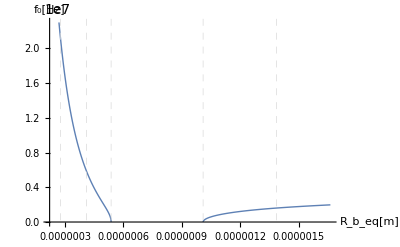

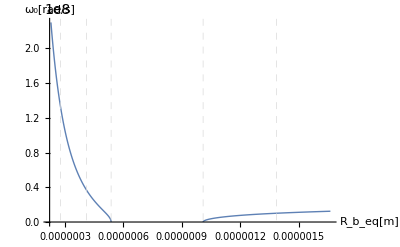

```mathematica
(*Natural frequency*)
freqnat[RL1_,Rb_]:=1/(2Pi)√((5(1-(Rb/RL1)^3)^2)/(5-9 Rb/RL1+5(Rb/RL1)^3-(Rb/RL1)^6)*3/(ρ0*(Rl0^3-Rb0^3)/(RL1^3-Rb^3)*Rb^2)*(3/(4Pi)*(mg*Rg*T)/Rb^3-(2σ)/(3Rb)+(Ev*Rb^3)/(Rl0^3-Rb0^3))) 

ω0in2[Rb_]:=(5*(1-(Rb/RL1[Rl0,Rb0,Rb])^3)^2)/(5-9 Rb/RL1[Rl0,Rb0,Rb]+5(Rb/RL1[Rl0,Rb0,Rb])^3-(Rb/RL1[Rl0,Rb0,Rb])^6)*3/(ρ0*(Rl0^3-Rb0^3)/(RL1[Rl0,Rb0,Rb]^3-Rb^3)*Rb^2)*(3/(4Pi)*(mg*Rg*T)/Rb^3-(2*σ)/(3*Rb)+(Ev*Rb^3)/(Rl0^3-Rb0^3));
Plot[{
freqnat[RL1[Rl0,Rb0,Rb],Rb]

},
{Rb,0,1.2*RadiusC},
AxesLabel->{"R_b_eq[m]","f_0[Hz]"},
LabelStyle->Directive[Black,Bold,16],
GridLinesStyle->Directive[Dashed],

PlotRange->{{0.8Rb0,1.2*RadiusC},{0.95Rb0*0,2.3*10^7}},

PlotStyle->{
Thickness[Large]
},
PlotPoints->1000,
(*AxesOrigin->{0*10^-6,0*10^-6},*)
GridLines->{{Rb0,RadiusA,RadiusB,RadiusD ,RadiusC  },{}}
]


Plot[{
(ω0in2[Rb])^0.5

},
{Rb,0,1.2*RadiusC},
AxesLabel->{"R_b_eq[m]","ω_0[rad/s]"},
LabelStyle->Directive[Black,Bold,16],
GridLinesStyle->Directive[Dashed],

PlotRange->{{0.8Rb0,1.2*RadiusC},{0.95Rb0*0,2.3*10^8}},

PlotStyle->{
Thickness[Large]
},
PlotPoints->1000,
(*AxesOrigin->{0*10^-6,0*10^-6},*)
GridLines->{{Rb0,RadiusA,RadiusB,RadiusD ,RadiusC  },{}}
]
```

```mathematica
freqnat[RL1[Rl0,Rb0,Rb0],Rb0]
(ω0in2[Rb0])^0.5
```

2.13125×10^7

1.3391×10^8

```mathematica
Plot[{
Rb/RL1[Rl0,Rb0,Rb]
},
{Rb,0,1.1*RadiusC},
AxesLabel->{"R_b_eq[m]","a=R_b_eq/R_L1_eq"},
LabelStyle->Directive[Black,Bold,16],
GridLinesStyle->Directive[Dashed],

PlotRange->{{0.0Rb0,1.1RadiusC},{0,0.04}},

PlotStyle->{
Thickness[Large]
},
PlotPoints->1*Npoints,
(*AxesOrigin->{0*10^-6,0*10^-6},*)
GridLines->{{Rb/.NSolve[D[f[Rb],Rb]==0,Rb][[3]],Rb0,RadiusA,RadiusB,RadiusD ,RadiusC,190RadiusC  },{1}}
]
```

```mathematica
0.8Rl0
RL1[Rl0,Rb0,1.2*RadiusC]
```

0.000032

0.0000400021

```mathematica
Plot[{
Rb0/(10^-6*RL11)
},
{RL11,0,10^6*RL1[Rl0,Rb0,130*RadiusC]},
AxesLabel->{"R_L1_eq[μm]","R_b0/R_L1_eq"},
LabelStyle->Directive[Black,Bold,16],
GridLinesStyle->Directive[Dashed],

PlotRange->{{10^6*0.9Rl0,10^6*RL1[Rl0,Rb0,130*RadiusC]},{0,0.01}},

PlotStyle->{
Thickness[Large]
},

(*AxesOrigin->{0*10^-6,0*10^-6},*)
GridLines->{{10^6*Rl0},{}}
]
```

```mathematica
Manipulate[{Rb0/RL11},{RL11,0.9Rl0,RL1[Rl0,Rb0,130*RadiusC]}]
```

```mathematica
Rl0*1.
```

0.00004

```mathematica
f[Rb_]:=Rb/((Rb^3+(Rl0^3-Rb0^3)/Ev*(P0-Pv-(3*mg*Rg*T)/(4*Pi*Rb^3)+Ev+(2*σ)/Rb))^(1/3))
```

```mathematica
(Rb/.NSolve[D[f[Rb],Rb]==0,Rb][[3]])/Rb0
Rb/.NSolve[D[f[Rb],Rb]==0,Rb][[3]]
```

0.0827325

2.28468×10^-8

```mathematica
D[f[Rb],Rb]==0
```

-(Rb (2.90909×10^-23 ((3.95081×10^-14)/Rb^4-0.14572/Rb^2)+3 Rb^2))/(3 (2.90909×10^-23 (2.2001×10^9-(1.31694×10^-14)/Rb^3+0.14572/Rb)+Rb^3)^(4/3))+1/((2.90909×10^-23 (2.2001×10^9-(1.31694×10^-14)/Rb^3+0.14572/Rb)+Rb^3)^(1/3))==0

```mathematica
(*Frequency response*)
```

```mathematica
Apm[Rb_]:=(5*(1-(Rb/RL1[Rl0,Rb0,Rb])^3)^2)/(5-9 Rb/RL1[Rl0,Rb0,Rb]+5(Rb/RL1[Rl0,Rb0,Rb])^3-(Rb/RL1[Rl0,Rb0,Rb])^6)*1/(ρ0*(Rl0^3-Rb0^3)/(RL1[Rl0,Rb0,Rb]^3-Rb^3)*Rb^2)*(3*Ev*RL1[Rl0,Rb0,Rb]^3)/(Rl0^3-Rb0^3);  
(*(1+9/5*Rb/RL1[Rl0,Rb0,Rb])*3/(ρ0*(Rl0^3-Rb0^3)/(RL1[Rl0,Rb0,Rb]^3-Rb^3)*Rb^2)*Ev*RL1[Rl0,Rb0,Rb]^3/Rl0^3*)
Bpm[Rb_]:=(20*μ*(1-(Rb/RL1[Rl0,Rb0,Rb])^3))/(5-9 Rb/RL1[Rl0,Rb0,Rb]+5(Rb/RL1[Rl0,Rb0,Rb])^3-(Rb/RL1[Rl0,Rb0,Rb])^6)*1/(ρ0*(Rl0^3-Rb0^3)/(RL1[Rl0,Rb0,Rb]^3-Rb^3)*Rb^2);  
Cpm[Rb_]:=3/2*(1+3*Rb/RL1[Rl0,Rb0,Rb]+(Rb/RL1[Rl0,Rb0,Rb])^2)/(5+6*Rb/RL1[Rl0,Rb0,Rb]+3(Rb/RL1[Rl0,Rb0,Rb])^2+(Rb/RL1[Rl0,Rb0,Rb])^3)*RL1[Rl0,Rb0,Rb]^2/Rb^2;    
ω0in2[Rb_]:=(5*(1-(Rb/RL1[Rl0,Rb0,Rb])^3)^2)/(5-9 Rb/RL1[Rl0,Rb0,Rb]+5(Rb/RL1[Rl0,Rb0,Rb])^3-(Rb/RL1[Rl0,Rb0,Rb])^6)*3/(ρ0*(Rl0^3-Rb0^3)/(RL1[Rl0,Rb0,Rb]^3-Rb^3)*Rb^2)*(3/(4Pi)*(mg*Rg*T)/Rb^3-(2*σ)/(3*Rb)+(Ev*Rb^3)/(Rl0^3-Rb0^3));
doubledelta[Rb_]:=(20*μ*(1-(Rb/RL1[Rl0,Rb0,Rb])^3))/(5-9 Rb/RL1[Rl0,Rb0,Rb]+5(Rb/RL1[Rl0,Rb0,Rb])^3-(Rb/RL1[Rl0,Rb0,Rb])^6)*1/(ρ0*(Rl0^3-Rb0^3)/(RL1[Rl0,Rb0,Rb]^3-Rb^3)*Rb^2);
Hclassic[Rb_,ω_]:=√(1/((ω0in2[Rb]-ω^2)^2+ω^2*(doubledelta[Rb])^2));
Hmodern[Rb_,ω_]:=√(((Apm[Rb]+Cpm[Rb]*ω^2)^2+ω^2*Bpm[Rb]^2)/((ω0in2[Rb]-ω^2)^2+ω^2*(doubledelta[Rb])^2));
fomegafactor[Rb_,ω_]:=√((Apm[Rb]+Cpm[Rb]*ω^2)^2+ω^2*Bpm[Rb]^2);
func1[Rb_]:=((5(1-(Rb/RL1[Rl0,Rb0,Rb])^3)^2)/(5-9 Rb/RL1[Rl0,Rb0,Rb]+5(Rb/RL1[Rl0,Rb0,Rb])^3-(Rb/RL1[Rl0,Rb0,Rb])^6)*3/(ρ0*(Rl0^3-Rb0^3)/(RL1[Rl0,Rb0,Rb]^3-Rb^3)*Rb^2)*(3/(4Pi)*(mg*Rg*T)/Rb^3-(2σ)/(3Rb)+(Ev*Rb^3)/(Rl0^3-Rb0^3))(*-((10μ*(1-(Rb/RL1[Rl0,Rb0,Rb])^3))/(5-9 Rb/RL1[Rl0,Rb0,Rb]+5(Rb/RL1[Rl0,Rb0,Rb])^3-(Rb/RL1[Rl0,Rb0,Rb])^6)*1/(ρ0*(Rl0^3-Rb0^3)/(RL1[Rl0,Rb0,Rb]^3-Rb^3)*Rb^2))^2*))^0.5
```

```mathematica
z1=5*10^6;
t2=(ω0in2[Rb0])^0.5;
Show[
{Plot3D[{Hmodern[Rb,ω]},
{Rb,0,1.2RadiusC},
{ω,0,t2},
AxesLabel->Automatic,
PlotStyle->{
Thickness[Large]
},
MaxRecursion->4,
PlotPoints->70,
PlotRange->{0,z1},
ColorFunction->"Rainbow",
PlotLegends->Automatic,
LabelStyle->Directive[Black,Bold,16],
PlotLabel->"B/A"
],
ParametricPlot3D[{Rb0,ω,z},{ω,0,t2},{z,0,t2},PlotStyle->Directive[Opacity[0.5],Blue, Specularity[Blue,90]]],
ParametricPlot3D[{RadiusB,ω,z},{ω,0,t2},{z,0,t2},PlotStyle->Directive[Opacity[0.5],Red, Specularity[Red,90]]],
ParametricPlot3D[{RadiusD,ω,z},{ω,0,t2},{z,0,t2},PlotStyle->Directive[Opacity[0.5],Green, Specularity[Green,90]]]
}]
```

-Graphics3D-

```mathematica
Show[
Plot3D[{fomegafactor[Rb,ω]},
{Rb,0,1.2RadiusC},
{ω,0,t2},
AxesLabel->Automatic,
PlotStyle->{
Thickness[Large]
},
PlotPoints->70,
MaxRecursion->4,
PlotRange->{0,1.3*10^21},
ColorFunction->"Rainbow",
PlotLegends->Automatic,
(*Filling->Bottom,*)
LabelStyle->Directive[Black,Bold,16],
PlotLabel->"|f(ω)|"
],
ParametricPlot3D[{Rb0,ω,z},{ω,0,30*10^7},{z,0,1.3*10^21},PlotStyle->Directive[Opacity[0.5],White, Specularity[White,70]]]]
```

-Graphics3D-

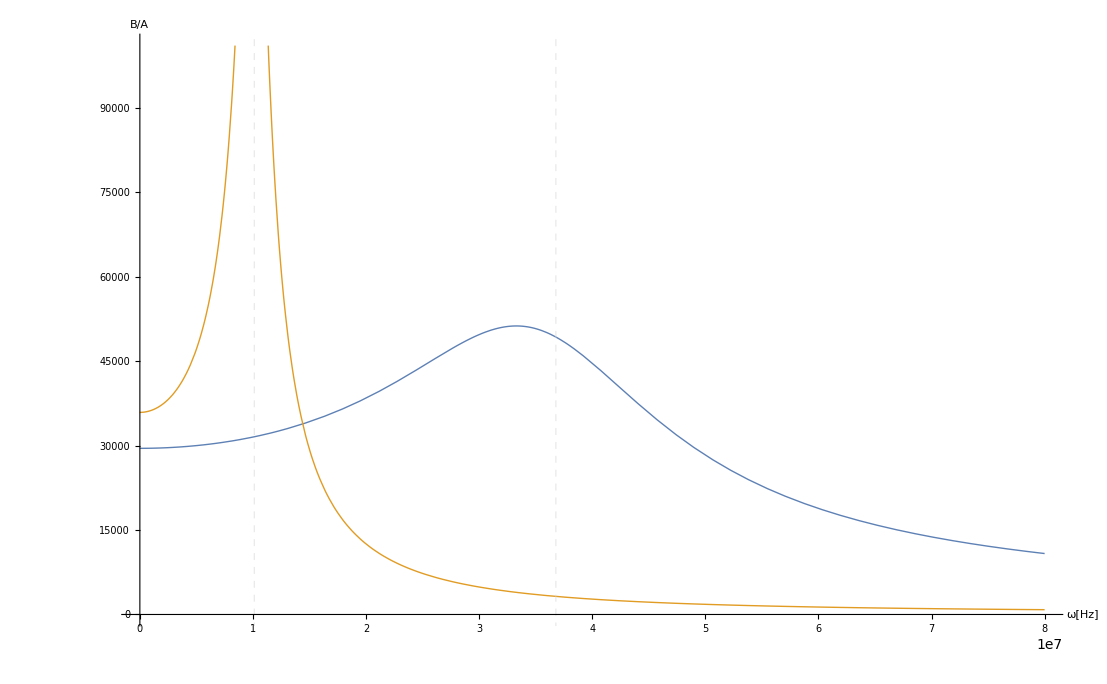

```mathematica
Plot[{
(*Hmodern[Rb0,ω],*)
Hmodern[RadiusA,ω],
(*H[RadiusB,ω],
H[RadiusD,ω]*)
Hmodern[RadiusC,ω]
},
{ω,0,80*10^6},
AxesLabel->{"ω[Hz]","B/A"},
LabelStyle->Directive[Black,Bold,16],
GridLinesStyle->Directive[Dashed],
(*PlotRange->{{0.0,80*10^6},{0,2*10^5}},*)
(*PlotRange->{{0.0,80*10^7},{0,43900}},*)
(*PlotRange->{{0.0,80*10^-2},{0,10^28}},*)
GridLines->{{func1[RadiusA],func1[RadiusC]},{}},
PlotStyle->{
Thickness[Large]
},
AxesLabel->Automatic
]
```

```mathematica
Manipulate[{Hmodern[Rb0,ω],
Hmodern[RadiusA,ω],
Hmodern[RadiusB,ω],
Hmodern[RadiusD,ω],
Hmodern[RadiusC,ω]},{ω,0,30*10^3}]
```